Computational implications of the third law of Thermodynamics on elementary cellular automata
By Gianmarco Morbelli
University of Groningen

The Third Law of Thermodynamics asserts the impossibility to reduce the entropy of a system to its absolute-zero value in a finite number of steps. The aim of this project is to investigate how the third law can be understood within the category of computational programs such as cellular automata. Simple computational experiments on cellular automata are set up such that perturbations, defined as changing the color of a set of cells at certain steps in the iteration, are applied during the evolution of the system. The goal is to achieve, with the least amount of perturbations, a final state consisting of cells all of the same colour (“Local  consensus”), as they neatly correspond to states of minimum entropy, thus capturing the essence of the Third Law. It is argued that the principle of computational irreducibility prevents us from knowing a priori which conditions lead to a decrease in entropy. Thus, the loss of information about which steps to perform to reach a zero entropy state is conjectured to be what we perceive as the Third Law of Thermodynamics. Possible future path of investigation may be to carry over this procedures to higher dimensional cellular automata and to more general rewriting systems such as hypergraph rewriting.

## Introduction

The Third Law of Thermodynamics can be formulated as “It is impossible for any process, no matter how idealized, to reduce the entropy of a system to its absolute-zero value in a finite number of operations.” [1].  A meaningful question arises when trying to carry over this rule to simple models such as cellular automata (CA), that is whether the law holds fundamentally also on discrete models.  Cellular automata have been studied extensively in literature and they represent optimum models to apply in order to understand complex behaviours in more general physical systems (see e.g. justifications for usage of CA in Thermodynamics in [2], [3]).

### Entropy of Cellular Automata

In order to devise a toy model to exploit the properties of the Third Law, it is essential to give a definition of entropy for a CA state. We will adopt the Shannon Entropy used in information theory:

```mathematica
entropyCA[p_List] :=-Sum[p[i].Log[2,p[i]], i]
```

where p[i] represents the probability of a white/black cell. It, thus, follows that a certain state of minimum entropy will correspond to all cells either being white or black.

### General Procedure

The main objective of this project is to find a procedure to perturb the evolution of a cellular automaton by driving it to reach a zero entropy state in a finite number of iterations and with the minimum effort required.  Firstly, the simpler case involving additive rules is studied: the first task is to find the set of states for which a given rule evolves to a zero state spontaneously and successively, a function is defined so that the minimum amount of perturbations is used to drive the cellular automaton to a zero state.The more general non-linear case is then investigated, and its implication with the principle of computational irreducibility are discussed.

#### Code Formatting

All the necessary code used in this project to generate plots/figures and functions can be found in the relevant sections by expanding the inputs. Additionally code and plots not essential to the presentation of this notebook can be found in the appendix.

## Perturbations

### Functional Perturbations

In this context, perturbations of  a current state of a cellular automaton are defined as temporary changes of cell states during the evolution of the automata: as an example, we could decide to swap the color of a set of cells at some time t and study how the perturbation affects the overall evolution. We define a function to perform this:

```mathematica
substitutionCAFunctional[rule_,init_, t_, sub_]:=With[{sublist=Flatten[Join[ConstantArray[rule,sub[[2]]-1],PadRight[{#1},  #2, rule]&@@@ Partition[Riffle[sub[[;;;;2]],(#2-#1)&@@@Partition[Join[sub, {rule, t+1}][[2;;;;2]] ,2,1]],2]],1]},FoldList [CellularAutomaton[#2, #1, {{{1}}}]&,init,sublist]]
```

The list sub must be of the form {f1, t1, f2, t2, etc..} where each f represents a transformation rule compatible with the CellularAutomaton built-in function, and each t refers to the time-step of application of the respective transformation rule. 
As an example consider the evolution of the famous rule 30 which displays class 3 behaviour. Suppose we want to introduce a slight perturbation in the evolution of the CA above. We can perturb the system by inputting that only at state 10 it should act as a rule 90 cellular automata, while the subsequent evolutions return to applications of rule 30 (the cells that evolve differently after the perturbation is applied are colored red):

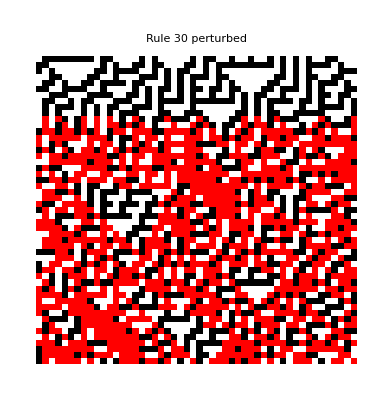

```mathematica
SeedRandom[852];
randomInit = RandomInteger[1,50];
colorplot=MapAt[Red&,substitutionCAFunctional[30,randomInit, 50,{{Mod[#[[1]]+#[[3]],2]&,{},1},10}],Position[Partition[MapThread[Equal,{Flatten[substitutionCAFunctional[30,randomInit, 50,{{Mod[#[[1]]+#[[3]],2]&,{},1},10}]],Flatten[CellularAutomaton[30,randomInit, 50 ]]}],50],False]];
 GraphicsRow[{ArrayPlot[CellularAutomaton[30,randomInit ,50],PlotLabel->"Rule 30" ],ArrayPlot[colorplot,PlotLabel->"Rule 30 perturbed"]}, ImageSize->Full]
```

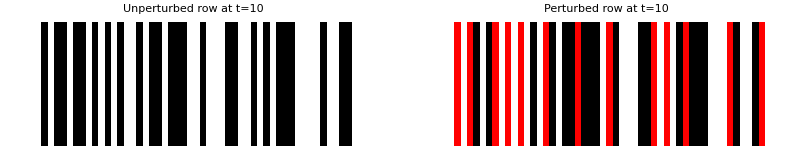

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[30,randomInit ,{{10}}],PlotLabel->"Unperturbed row at t=10" ],ArrayPlot[{colorplot[[11]]},PlotLabel->"Perturbed row at t=10"]}, ImageSize->Full]
```

### n-Flip Perturbations

More specific to the project problem, we define a function called nFlipCA which performs n-cell flips (i.e. color changes from white to black and vice versa) for a given rule at a given iteration time. The scope is to apply this function once the knowledge about which cells to perturb is obtained. As before, we  highlight in red every cell which is different from the normal evolution after the perturbation is applied:

```mathematica
nflipCA[rule_,init_,t_,fun_,position_, tsub_]:=If[position=={},CellularAutomaton[rule,init,t],If[tsub==0,CellularAutomaton[rule, fun[CellularAutomaton[rule,init,{{{tsub}}}],position], t],Module[{newstate=fun[CellularAutomaton[rule,init,{{{tsub}}}],position]},Join[CellularAutomaton[rule,init,tsub-1], {newstate}, CellularAutomaton[rule,newstate,{{1,t-tsub}}]]]]]
```

```mathematica
funswap[list_, position_]:=ReplacePart[list, (#-> 1-list[[#]])&/@position]

coloredArrayFull[rule_,init_,t_,flip_,timesub_]:=MapAt[Red&,flip[[(timesub+1);;]],Position[Partition[MapThread[Equal,{Flatten@flip[[(timesub+1);;]],Flatten@CellularAutomaton[rule, init, {{timesub,t}} ]}],Length[init]],False]]

plotColorFull[rule_,init_,t_,flip_,timesub_]:=GraphicsRow[({ArrayPlot[CellularAutomaton[rule,init,t], #],ArrayPlot[Join[flip[[;;timesub]],coloredArrayFull[rule,init,t,flip,timesub]],#]})&@@{ImageSize->Full}]
```

As an example, let us swap the color of the middle cell for rule 30 at time 25 during the evolution of 50 cells:

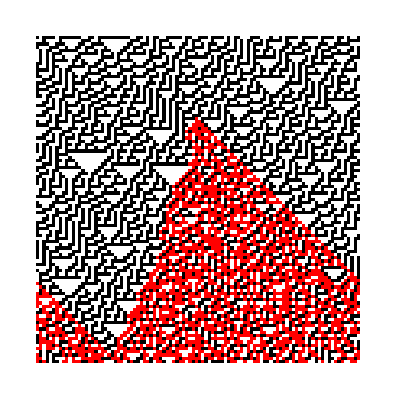
-Graphics-Rule 30: Unperturbed (left) vs Pertubed (right)

```mathematica
SeedRandom[567];
randominit11=RandomChoice[{.7,.3}->{1,0},100];
flip22=nflipCA[30,randominit11,100, funswap,{50},25];
 Labeled[plotColorFull[30, randominit11, 100,flip22,25], "Rule 30: Unperturbed (left) vs Pertubed (right)", Top]
```

Notice how the light cone (and thus the limit at which the information of the perturbation travels) extends clearly from the perturbed middle cell: due to the boundary conditions it, also, passes through the right “wall” of the cellular automata and affects the left hand side.

## Considering the Problem Within Linear Cellular Automata

### Finding the Kernel of Linear Rules

Considering elementary cellular automata, there exist only 8 linear/additive rules: {0, 60, 90, 102, 150, 170, 204, 240} [4]. Linear automata behave analogously to linear systems, in particular their overall evolution can be expressed as a linear combination of individual evolutions, where the additive operations is specific to the rule chosen. In mathematical terms, additive automata require that the evolution of arbitrary states α and β upon application of the rule    satisfies , where the symbol  denotes the additivity operation of the rule chosen [5].  Exploiting the similarity with linear systems, we can express a linear rule as a linear combination of its “basis” states, i.e. states where only one cell is black/active, while the remaining cells are set white:

```mathematica
basisAutomata[rule_, n_]:=Transpose[CellularAutomaton[rule, #, {{{1}}}]&/@Permutations[PadRight[{1}, n]]]
```

For rule 90, the 6-cell basis states evolve as follows:

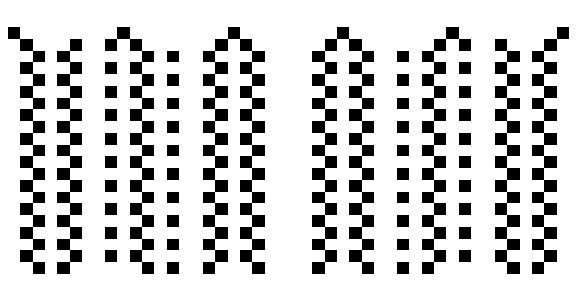

```mathematica
evolutionBasisStatesLCA[rule_, ncell_, t_, basisnumber_]:=CellularAutomaton[rule, #, t]&@Permutations[PadRight[{1}, ncell]][[basisnumber]];
showEvolution [rule_,ncell_, t_]:=GraphicsRow[Table[ArrayPlot[evolutionBasisStatesLCA[rule, ncell, t, i]],{i,1,ncell}],PlotLabel->HoldForm["Rule 90: Evolution of its Basis States"], ImageSize->Large]
showEvolution[90,6,20]
```

Notice how the basis states evolve in the same way, they only get shifted (a resemblance of the fact that the propagation operator is shift invariant).

By exploiting the tools of Linear Algebra, the evolution of the basis states for the case above can be cast in matrix form representing the rule transformation  as

```mathematica
evol =basisAutomata[90, 6]
```

{{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}}

```mathematica
MatrixForm[evol]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)

Given a number of cells    in 1D, finding the states for which the evolution leads to a zero state is now equivalent to finding the kernel of the transformation rule    for some powers  with  , where we can improve the efficiency of this function by adding the constraint that the computations should stop when the kernel of   is found equal to the kernel of , as we assume that the kernel for higher powers won’t change anymore. Additionally, since many states appear multiple times in the kernel of higher matrix powers, we thus remove these duplicates from the final set of kernels:

```mathematica
solveKernel[rule_,ncell_, npower_, nsolutions_]:=Module[{varlist =Table[Unique["x"],{ncell}]},(varlist/.#)&/@FindInstance[MatrixPower[Transpose[CellularAutomaton[rule, #, {{{1}}}]]&/@Permutations[PadRight[{1}, ncell]],npower].varlist== ConstantArray[0,ncell], varlist,nsolutions, Modulus->2]]
```

```mathematica
solvekernelstop[rule_,ncell_,nsolutions_]:=Last@Reap@Do[Sow[solveKernel[rule,ncell, i,nsolutions]];If[solveKernel[rule,ncell, i,nsolutions]==solveKernel[rule,ncell, i+1,nsolutions],Break[]],{i,1,2^ncell}]

kernelwoduplicate[kernel_]:=DeleteCases[Module[{f},f[x_]:=(f[x]=Sequence[];x);
Map[f,kernel,{2}]],{{}...},Infinity];
```

Let’s test it and find the kernel for rule 90 for 20 cells:

Considering the linear rule 90, we can display some of these states belonging to the null space of the rule transformation:

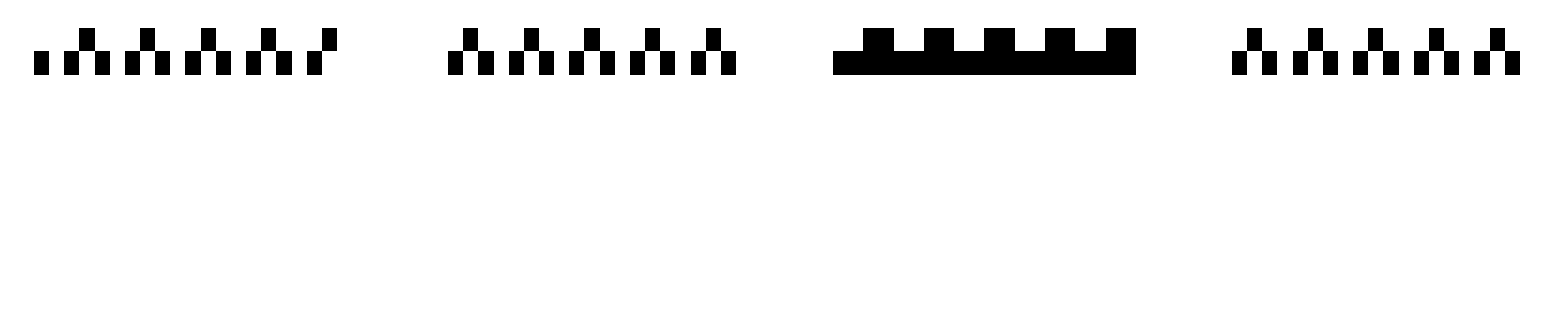
-Graphics-Some Rule 90 Null Space States

```mathematica
plotStates[rule_,kernel_]:=GraphicsRow[ArrayPlot[CellularAutomaton[rule,(Catenate@kernel)[[#]], 10]]&/@Range[5, 8], ImageSize->Full]
kernelrule90simplifiednodup =kernelwoduplicate[First@solvekernelstop[90,20, 100000]];
Labeled[plotStates[90, kernelrule90simplifiednodup], "Some Rule 90 Null Space States", Top]
```

### Solving for Linear Cellular Automata

We found an analytical method to explore the kernel of linear cellular automata and thus find the states which map to zero after a certain number of iterations. The task now is to implement an algorithm/function that given any initial condition manages to find the minimum amount of the cells to perturb so that the cellular automata will map to zero by using the knowledge of the states contained in the null space of the linear rule.

```mathematica
swapFunctionLinearAutomata[rule_, init_, t_]:=Module[{kernel= kernelwoduplicate[First@solvekernelstop[rule,Length[init], 100000]]},Module[ {nearestf = Nearest[Catenate@kernel -> All,DistanceFunction->HammingDistance]}, Module[{firstpositionsmall =Ordering[#["Distance"]&/@Catenate[nearestf[CellularAutomaton [rule, init, t]]],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@Catenate[nearestf[CellularAutomaton[rule, init,t]]])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1] },If[First@firstpositionsmall-1<0,CellularAutomaton[rule, init, t], nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1]]]]]]
```

```mathematica
swapFunctionLinearAutomataColored[rule_, init_, t_]:=Module[{kernel= kernelwoduplicate[First@solvekernelstop[rule,Length[init], 100000]]},Module[ {nearestf = Nearest[Catenate@kernel -> All,DistanceFunction->HammingDistance]}, Module[{firstpositionsmall =Ordering[#["Distance"]&/@Catenate[nearestf[CellularAutomaton [rule, init, t]]],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@Catenate[nearestf[CellularAutomaton[rule, init,t]]])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1]  },If[First@firstpositionsmall-1<0, CellularAutomaton[rule, init, t], ReplacePart[nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1], {{First@firstpositionsmall,#}&/@positionswap -> Red}]]]]]]
```

We can test the function for the whole range of additive elementary rules (as usual, the red cells correspond to the perturbations applied):

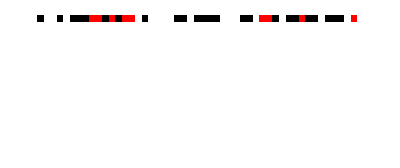
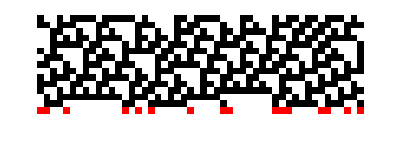
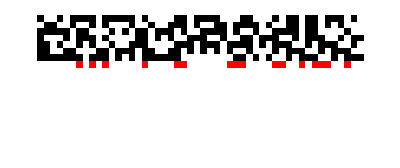
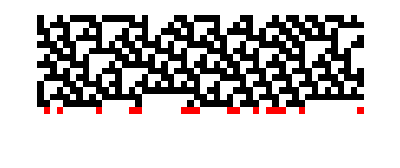
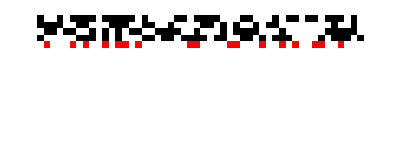
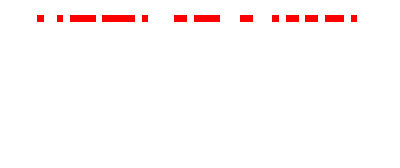
{-Graphics-Rule 0,-Graphics-Rule 60,-Graphics-Rule 90,-Graphics-Rule 102,-Graphics-Rule 150,-Graphics-Rule 170,-Graphics-Rule 204,-Graphics-Rule 240}

```mathematica
linearRules = {0,60,90,102,150,170,204,240};
SeedRandom[561];
randinit = RandomInteger[1,50];

plotSolution[rule_, init_, t_]:=GraphicsRow[{ArrayPlot[CellularAutomaton[rule,init,t]], ArrayPlot[swapFunctionLinearAutomata[rule,init,t]]},PlotLabel->StringJoin["Rule ", ToString[rule]],ImageSize->Large]

plotSolutionColored[rule_, init_, t_]:=Labeled[GraphicsRow[{ArrayPlot[CellularAutomaton[rule,init,t]], ArrayPlot[swapFunctionLinearAutomataColored[rule,init,t]]},ImageSize->Large],StringJoin["Rule ", ToString[rule]], Top]

plotSolutionColored[#,randinit, 20]&/@linearRules
```

Computations for cellular automata with up to 50 cells can be easily carried out, showing how indeed it is not needed to evaluate all the    states and thus reduce the computational effort required to solve the problem. Linear rules display nested and recurring patterns, and as such they are computationally reducible. This implies that it is possible to skip ahead of the computations and find the states that do map to zero in a time less than    where  is the number of cells. Due to their computation reducibility, it is thus not surprising that the these rules do not always obey the Third Law of Thermodynamics.

## Considering the Problem Within Non-Linear Cellular Automata

### Dynamical System Approach

It comes without a surprise that the nonlinear case is fundamentally more complicated to solve, and in the end we will see that it comprises to the fact that computational irreducibility does not allow us to know in advance which states drive the cellular automata to a zero state.
The approach followed consists, firstly, in defining a so called attractive surface containing the set of states that map to zero after n- steps for a given rule. We introduce the terminology n-iter dimension to specify that the n-iter dimensional attractive surface for a given rule is comprised of states that evolve to a zero entropy state in 1 up to n iterations.
We will now consider the simplest case of 1-iter dimensional attractive surfaces:

```mathematica
findStates1d[rule_,ncell_]:=Module[{zerostates=Select[PadLeft[IntegerDigits[#,2],ncell]&/@Range[0,2^ncell-1],MatchQ[CellularAutomaton[rule, #,{{{1}}}],{0..}]&]},If[MemberQ[zerostates,ConstantArray[0,ncell] ], zerostates,Join[{ConstantArray[0,ncell]},zerostates]]]
```

As an example, the states in the attractive surface for rule 20 and for 4 cells are given by:

```mathematica
findStates1d[20,4]
```

{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

A clean and effective way to display these states is by plotting the state transition diagrams:

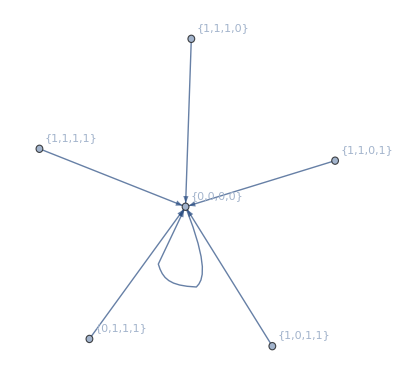

```mathematica
stateDiagramZeroStates[rule_,ncell_]:= GraphPlot[#->CellularAutomaton[rule,#]&/@findStates1d[rule,ncell], VertexLabels->Automatic, DirectedEdges-> True, GraphLayout->"SpringElectricalEmbedding"]
stateDiagramZeroStates[20,4]
```

For instance, consider the state diagram of all the states for rule 20 and 4 cells (where the zero state has been labelled by “0”):

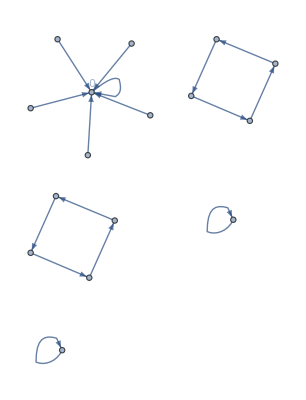

```mathematica
statesTransition[rule_,ncell_]:=GraphPlot[#->CellularAutomaton[rule,#]&/@Tuples[{0,1}, ncell], VertexLabels->{{0..}-> Placed["0",{0.5,2}]},DirectedEdges->True, GraphLayout->"SpringEmbedding"]
statesTransition[20,4]
```

From the diagrams above, it can be clearly seen that some states remain disconnected from the attractive surface, and thus this will prevent them to spontaneously evolve to the zero state. It thus follows that the state transition diagrams give a nice visual formulation of the problem in question: acting as a Maxwell Demon, the task is to define a procedure which takes states not connected to the zero states and perturbs them so that they eventually enter the attractive surface. We now have the goal to study and analyze the behaviour of these disconnected state, and eventually learn when to perturb them at the right time and positions during the evolution of the cellular automata.
A visual example of the procedure explained is given below, where for rule 20 and 4 cells one state outside the attractive surface is perturbed to reach the zero state:

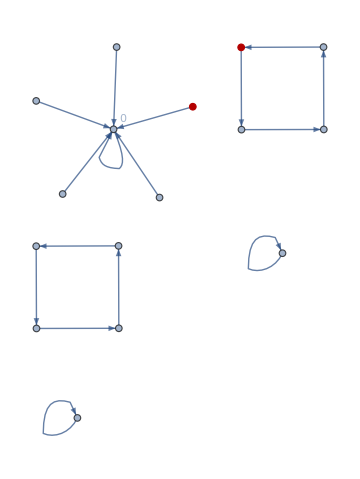
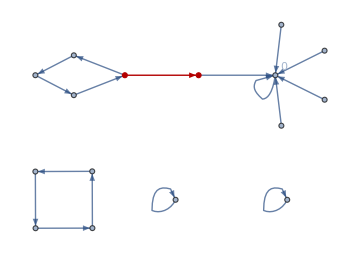
-Graphics-→-Graphics-

```mathematica
rule={{0,0},{1,9},{2,3},{3,8},{4,6},{5,5},{6,1},{7,0},{8,12},{9,4},{10,10},{11,0},{12,2},{13,0},{14,0},{15,0}}->{{0,0},{1,9},{2,3},{3,8},{4,6},{5,5},{6,1},{7,0},{8,12},{9,4},{10,10},{11,0},{12,2},{13,0},{14,0},{15,0},{6,13}};
inputGraph=Graph[DirectedEdge@@@First[rule], VertexLabels->{0-> "0"}];
outputGraph=Graph[DirectedEdge@@@Last[rule], VertexLabels->{0-> "0"}];
HighlightGraph[inputGraph,{6,13}, ImageSize->Medium]->HighlightGraph[outputGraph,Subgraph[outputGraph,{6,13}], ImageSize->Medium]
```

### Hamming Entropy

The evolution of a certain state within the possible    states can be characterized by a sort of Hamming entropy, that is we attribute to the state  Hamming distances with respect to the states in the attractive surfaces and observe how these distances change during the evolution of the cellular automata. Introducing the concept of Hamming distance (used more naively in the linear case before) leads to the benefit that it shows effectively the number of different bits a state possesses with respect to the states in the attractive surface. But these bits differences are exactly the number of  perturbations to apply in order for the cellular automata to reach the zero state.

For instance, considering rule 51 with 3 cells, the state {0,0,1} evolves for 5 steps as follows:

```mathematica
attractiveSurface[rule_,ncell_]:=Nearest[findStates1d[rule,ncell] -> All,DistanceFunction->HammingDistance]

evolutionStatenEntropynsteps[rule_,ncell_,staten_,nsteps_]:=attractiveSurface[rule,ncell][#]&/@CellularAutomaton[rule,Tuples[{0,1},ncell][[staten]], nsteps]

hammingDistanceList[rule_,ncell_,staten_,nsteps_]:=#["Distance"]&/@Catenate@evolutionStatenEntropynsteps[rule,ncell,staten,nsteps]
```

We actually want to select only sublist of length 1 as we are interested in the distance from the attractive states and not from the states themselves.

```mathematica
evolutionStatenEntropynstepsnodupli[rule_,ncell_,staten_,nsteps_]:=Module[{evol=evolutionStatenEntropynsteps[rule,ncell,staten,nsteps]}, evol[[#,1]]&/@Range[Length[evol]]]

hammingDistanceListnodupli[rule_,ncell_,staten_,nsteps_]:=#["Distance"]&/@evolutionStatenEntropynstepsnodupli[rule,ncell,staten,nsteps]

evolutionStatenEntropynstepsnodupli[51,3, 2,5]
```

{<|Element→{0,0,0},Index→1,Distance→1|>,<|Element→{1,1,1},Index→2,Distance→1|>,<|Element→{0,0,0},Index→1,Distance→1|>,<|Element→{1,1,1},Index→2,Distance→1|>,<|Element→{0,0,0},Index→1,Distance→1|>,<|Element→{1,1,1},Index→2,Distance→1|>}

We can extract the Hamming distances only:

```mathematica
hammingDistanceListnodupli[51,3, 2,5]
```

{1,1,1,1,1,1}

### Study of Typical Behaviour

It is now possible to plot and analyze the behaviour of all the   states for    registers (i.e. number of cells) as they evolve with respect to their Hamming distances:

```mathematica
plotBehaviour[rule_,ncell_,nsteps_]:=(Module[{hamminglist=hammingDistanceListnodupli[rule,ncell,#,nsteps]&/@Range[2^ncell]},ListLinePlot[hamminglist,PlotLabel->StringJoin["Rule ",  ToString@ rule, " & " ,ToString[ncell], " cells"] ,AxesLabel->{"Time", "Hamming Distance"}]])
```

For instance, considering rule 30 for 10 cells, the states outside of the attractive surface display an intricate behaviour (each state is represented by  a line of different color):

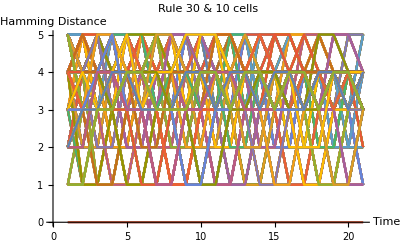

```mathematica
plotBehaviour[30,10, 20]
```

For graphical ease, a less cluttered plot is shown for rule 30 and 7 cells:

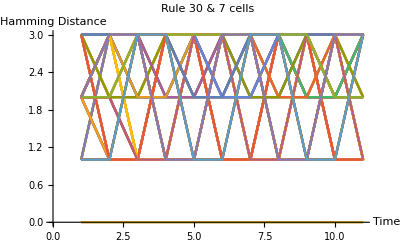

```mathematica
plotBehaviour[30,7, 10]
```

The behaviour shown it’s interesting: for this particular configuration most of the states do oscillate periodically with an amplitude of either 2 bits or 1 bit but never enter the attractive surface.

Following on this, we select some rules belonging to the four Wolfram classification and analyze how states tend to evolve with respect to the attractive surface.

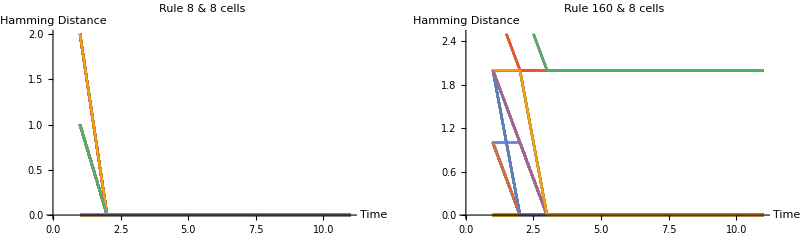
-Graphics-Class 1

```mathematica
ruleclass1 ={8,160 };
ruleclass2 = {10,138,164};
ruleclass3={30,122};
ruleclass4={41,54,106,110};
Labeled[GraphicsRow[plotBehaviour[#, 8, 10]&/@ruleclass1, ImageSize->Full], "Class 1", Top]
```

As expected, states evolving according to the class 1 rules we analyzed reach the attractive surface spontaneously, as characterized by their global uniform behaviour. Nevertheless, we can see in the right graph that there exist some states that stabilize at a fixed Hamming distance although rule is of class 1.  As an example take the state :

```mathematica
st=Tuples[{0,1}, 8][[88]]
```

{0,1,0,1,0,1,1,1}

which indeed correspond to the non-uniform but periodic evolution

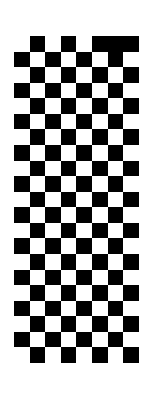

```mathematica
ArrayPlot@CellularAutomaton[160,st,20]
```

Notice that if we consider class 1 rule where the final pattern reaches black cells global consensus (such as rule 239 which is the black-white equivalent to rule 8) we obtain the opposite pattern, as the maximum Hamming distance from the zero state is indeed reached by the black state:

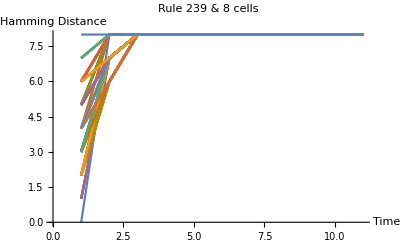

```mathematica
plotBehaviour[239, 8,10]
```

Analysis of class 2 rules that typically show periodic behaviour:

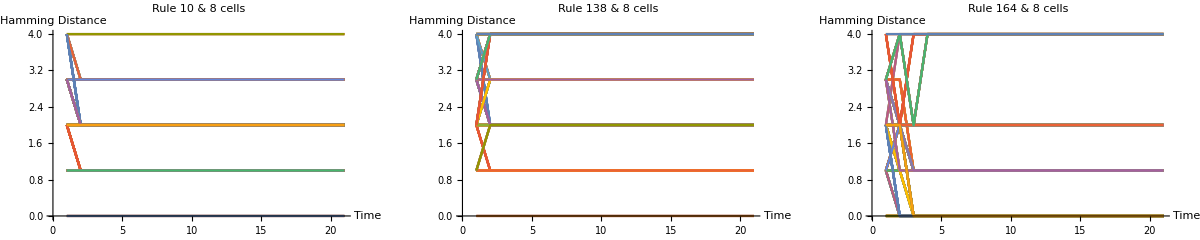
-Graphics-Class 2

```mathematica
Labeled[GraphicsRow[plotBehaviour[#, 8, 20]&/@ruleclass2, ImageSize->Full ], "Class 2", Top]
```

For class 2 rules most states tend to asymptotically stabilize at a fixed hamming distance/entropy from the attractive surface. This is reasonable as class 2 rules display periodic behavior, and as such the states get visually shifted along the cells as they evolve, but their bit difference/Hamming distance to the zero states is, indeed, unaffected.

We repeat the same procedure for class 3 rules:

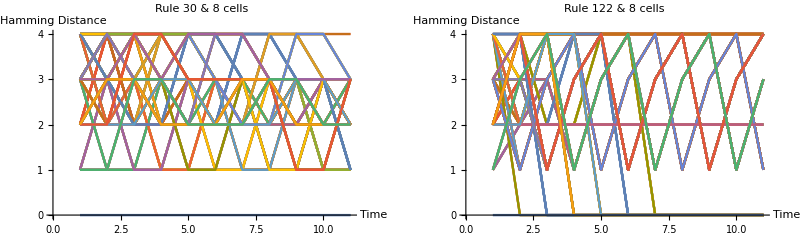
-Graphics-Class 3

```mathematica
Labeled[GraphicsRow[plotBehaviour[#, 8, 10]&/@ruleclass3, ImageSize->Full], "Class 3", Top]
```

Again, not surprisingly, class 3 rules display much more chaotic behaviour. It appears that after a brief complex transient response (where some states do also manage to enter the attractive surface) the states seems to eventually oscillate periodically.  A similar phenomenon is shown below by the entropic evolution of class 4 rules:

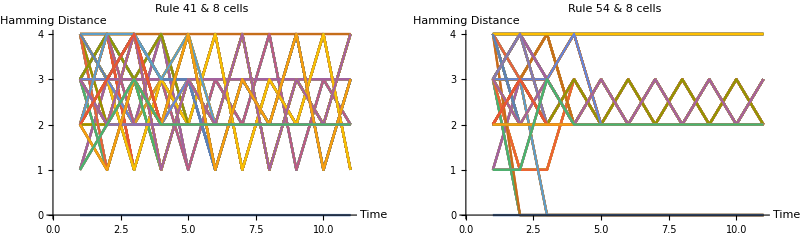
-Graphics-Class 4

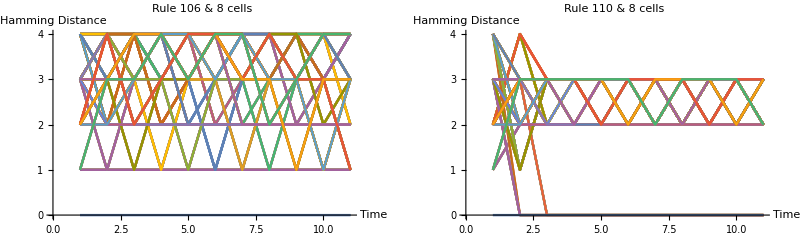

```mathematica
Labeled[GraphicsRow[plotBehaviour[#, 8, 10]&/@ruleclass4[[1;;2]], ImageSize->Full], "Class 4", Top]
GraphicsRow[plotBehaviour[#, 8, 10]&/@ruleclass4[[3;;4]], ImageSize->Full]
```

Notice in these case how some states also show metastable behaviour, that is they get closest to the attractive surface but then eventually drive away and stabilize at a fixed Hamming distance.

Additionally, we can infer how it seems that rules not always tend to evolve states to the highest entropy/distance possible. While this phenomenon may seem intuitive for class 1 and class 2 rules,  the pattern seems to apply surprisingly also at class 3 and 4 rules. It is conjectured thus that only a modest percentage of rules does evolve states to the maximum distance possible. We can easily test this for the whole range of elementary rules up to 10 cells:

```mathematica
biggestHammingDistance[rule_,ncell_,nsteps_]:=Max[Catenate@(hammingDistanceListnodupli[rule,ncell,#,nsteps]&/@Range[2^ncell])]
```

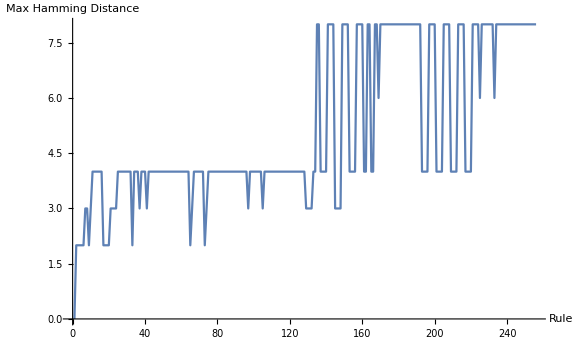

```mathematica
ListLinePlot[biggestHammingDistance[#,8,1]&/@Range[0,255],AxesLabel->{"Rule", "Max Hamming Distance"}, ImageSize->Large]
```

```mathematica
bigentropyrulesnccells2 =Hold[Module[{ncell=#},biggestHammingDistance[#,ncell,1]&/@Range[0,255]]&/@Range[1,10]]
```

Hold[(Module[{ncell=#1},(biggestHammingDistance[#1,ncell,1]&)/@Range[0,255]]&)/@Range[1,10]]

```mathematica
bigentropyrulesnccells ={{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null,1,Null},{0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,0,1,0,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,1,1,1,1,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null,2,Null},{0,1,1,2,1,2,1,2,1,1,1,3,1,3,1,3,1,2,1,2,1,2,1,2,1,3,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,1,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,1,1,2,1,2,1,2,2,2,3,Null,3,Null,3,Null,1,2,1,2,1,2,1,2,3,Null,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,2,2,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null,3,Null},{0,2,1,2,1,2,1,3,1,2,2,2,2,4,2,4,1,2,1,2,1,3,1,3,2,2,2,2,2,4,2,4,1,2,2,4,2,2,2,4,1,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,1,2,2,2,2,4,2,4,1,2,2,2,2,4,2,4,2,2,2,2,2,4,2,4,2,2,2,2,2,4,2,4,1,4,2,4,2,4,2,4,1,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,2,2,2,2,2,4,Null,2,2,2,2,4,Null,4,Null,2,2,2,2,4,Null,4,Null,2,2,2,2,4,Null,4,Null,2,2,4,Null,2,2,4,Null,3,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,2,2,2,2,4,Null,4,Null,2,2,2,2,4,Null,4,Null,2,2,2,2,4,Null,4,Null,2,2,2,2,4,Null,4,Null,3,Null,4,Null,4,Null,4,Null,3,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null,4,Null},{0,2,1,3,1,3,2,4,1,2,2,5,2,5,2,5,1,3,1,3,2,4,2,4,2,5,2,5,2,5,2,5,1,3,2,5,1,3,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,1,2,2,5,2,5,2,5,1,2,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,5,2,2,2,3,3,Null,5,Null,3,3,5,Null,5,Null,5,Null,2,3,2,3,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,3,Null,5,Null,3,Null,5,Null,4,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,3,3,5,Null,5,Null,5,Null,3,3,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,4,Null,5,Null,5,Null,5,Null,4,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null,5,Null},{0,2,2,3,2,4,2,4,2,2,2,3,3,6,3,6,2,3,2,3,2,4,2,4,2,3,2,3,3,6,3,6,2,3,3,6,2,4,3,6,2,3,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,2,2,2,3,3,6,3,6,2,2,2,3,3,6,3,6,2,3,2,3,3,6,3,6,2,3,2,3,3,6,3,6,2,3,3,6,3,6,3,6,2,3,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,3,6,2,2,2,3,3,4,3,4,3,3,3,3,6,Null,6,Null,2,3,2,3,3,4,3,4,3,3,3,3,6,Null,6,Null,4,4,6,Null,4,Null,6,Null,4,4,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,3,3,3,3,6,Null,6,Null,3,3,3,3,6,Null,6,Null,3,3,3,3,6,Null,6,Null,3,3,3,3,6,Null,6,Null,4,4,6,Null,6,Null,6,Null,4,4,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null,6,Null},{0,3,2,4,2,4,2,5,2,3,3,7,3,7,3,7,2,4,2,4,2,5,2,5,3,7,3,7,3,7,3,7,2,3,3,7,2,5,3,7,2,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,2,3,3,7,3,7,3,7,2,3,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,2,7,3,7,3,7,3,7,2,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,7,3,3,3,4,3,4,7,Null,4,4,7,Null,7,Null,7,Null,3,4,3,4,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,4,4,7,Null,5,Null,7,Null,5,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,4,4,7,Null,7,Null,7,Null,4,4,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,5,Null,7,Null,7,Null,7,Null,5,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null,7,Null},{0,3,2,4,2,4,3,6,2,3,4,4,4,8,4,8,2,4,2,4,3,6,3,6,4,4,4,4,4,8,4,8,2,4,4,8,3,4,4,8,3,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,2,3,4,4,4,8,4,8,2,3,4,4,4,8,4,8,4,4,4,4,4,8,4,8,4,4,4,4,4,8,4,8,3,8,4,8,4,8,4,8,3,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,3,3,3,4,4,4,8,Null,4,4,4,4,8,Null,8,Null,3,4,3,4,8,Null,8,Null,4,4,4,4,8,Null,8,Null,4,4,8,Null,4,4,8,Null,6,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,4,4,4,4,8,Null,8,Null,4,4,4,4,8,Null,8,Null,4,4,4,4,8,Null,8,Null,4,4,4,4,8,Null,8,Null,6,Null,8,Null,8,Null,8,Null,6,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null,8,Null},{0,3,3,5,3,5,3,6,3,3,4,9,4,9,4,9,3,5,3,5,3,6,3,6,4,9,4,9,4,9,4,9,3,4,4,9,3,5,4,9,3,4,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,3,3,4,9,4,9,4,9,3,3,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,3,4,4,9,4,9,4,9,3,4,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,4,9,3,3,3,5,4,6,4,6,5,5,9,Null,9,Null,9,Null,3,5,3,5,4,6,4,6,9,Null,9,Null,9,Null,9,Null,5,6,9,Null,5,Null,9,Null,6,6,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,5,5,9,Null,9,Null,9,Null,5,5,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,6,6,9,Null,9,Null,9,Null,6,6,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null,9,Null},{0,4,3,5,3,6,4,7,3,4,4,5,5,10,5,10,3,5,3,5,4,7,4,7,4,5,4,5,5,10,5,10,3,5,5,10,4,6,5,10,4,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,3,4,4,5,5,10,5,10,3,4,4,5,5,10,5,10,4,5,4,5,5,10,5,10,4,5,4,5,5,10,5,10,4,10,5,10,5,10,5,10,4,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,5,10,4,4,4,5,5,6,10,Null,5,5,5,5,10,Null,10,Null,4,5,4,5,10,Null,10,Null,5,5,5,5,10,Null,10,Null,6,6,10,Null,6,Null,10,Null,7,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,5,5,5,5,10,Null,10,Null,5,5,5,5,10,Null,10,Null,5,5,5,5,10,Null,10,Null,5,5,5,5,10,Null,10,Null,7,Null,10,Null,10,Null,10,Null,7,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null,10,Null}};
```

```mathematica
nullremoved2=DeleteCases[bigentropyrulesnccells, Null,2];
```

```mathematica
numberrulesupto10cellsmax=(Cases[nullremoved2[[#]], Max[nullremoved2[[#]]]])&/@Range[Length@nullremoved2];
```

```mathematica
numberrulesmaxupto10cell=Length /@numberrulesupto10cellsmax
```

{128,96,98,84,102,78,102,84,96,84}

Comparison to total cells

```mathematica
percentagemaxruleuptto10cells =N[numberrulesmaxupto10cell/256]
```

{0.5,0.375,0.382813,0.328125,0.398438,0.304688,0.398438,0.328125,0.375,0.328125}

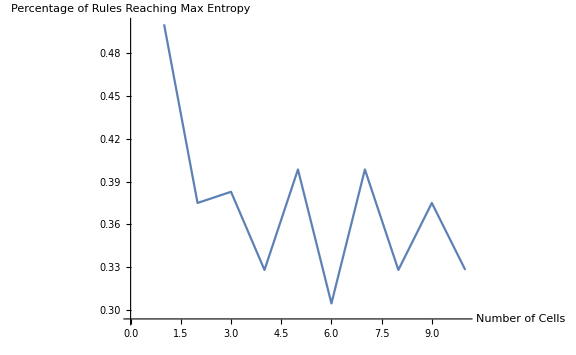

```mathematica
ListLinePlot[percentagemaxruleuptto10cells, AxesLabel->{"Number of Cells", "Percentage of Rules Reaching Max Entropy"}, ImageSize->Large ]
```

It appears that as the number of cells increases only about 1/3 of the rules evolve to states at maximum entropy from the attractive surface.

### Solving the Problem for the General Case

Knowing which states do map to zero for a given rule and number of cells, we can now implement a function that, given an initial state and an evolution time, it checks which state(s) within the evolution come closest to the states in the attraction surface. It thus then applies the necessary perturbations to this state in order to drive the cellular automata to a zero entropy state.

```mathematica
swapFunctionNonLinearAutomata[rule_, init_, t_]:=Module[{nstate =Position[Tuples[{0,1},Length[init]],init][[1,1]]},Module[{firstpositionsmall =Ordering[#["Distance"]&/@evolutionStatenEntropynstepsnodupli[rule,Length[init],nstate,t],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@evolutionStatenEntropynstepsnodupli[rule,Length[init],nstate,t])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1] },If[First@firstpositionsmall-1<0, CellularAutomaton[rule, init, t], nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1]]]]]
```

```mathematica
swapFunctionNonLinearAutomataColored[rule_, init_, t_]:=Module[{nstate =Position[Tuples[{0,1},Length[init]],init][[1,1]]},Module[{firstpositionsmall =Ordering[#["Distance"]&/@evolutionStatenEntropynstepsnodupli[rule,Length[init],nstate,t],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@evolutionStatenEntropynstepsnodupli[rule,Length[init],nstate,t])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1] },If[First@firstpositionsmall-1<0, CellularAutomaton[rule, init, t], ReplacePart[nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1], {{First@firstpositionsmall,#}&/@positionswap -> Red}]]]]]
```

As a nice example consider the evolution of rule 54 for 15 cells.

```mathematica
initrandom ={0,1,1,1,1,1,1,0,1,1,1,0,0,1,1};

rule5415cell=swapFunctionNonLinearAutomataColored[54,initrandom,20];

Labeled[GraphicsRow[{ArrayPlot@CellularAutomaton[54, initrandom, 20],ArrayPlot@rule5415cell}], "Rule 54 & 15 cells", Top]
```

-Graphics-

Displaying these with the aid of transition diagrams, the perturbation applied looks as follow:

```mathematica
graph = #->CellularAutomaton[54,#]&/@Tuples[{0,1}, 15];
left=FromDigits[graph[[#,1]],2]&/@Range[Length@graph];
right=FromDigits[graph[[#,2]],2]&/@Range[Length@graph];
zerostates=findStates1dniterwoduplicate[54,15,200][[2;;]];
zeroo=Catenate@zerostates;
vertices =FromDigits[zeroo[[#]],2]&/@Range[Length@zeroo];
ruless=MapThread[Rule, {left, right}];
rulessperturbed = Join[ruless, {34->0}];

(*Labeled[GraphPlot[HighlightGraph[ruless, Join[vertices, {34}]],ImageSize->Medium], "Unperturbed Rule 54 & 15 cells" , Top]-> Labeled[GraphPlot[HighlightGraph[rulessperturbed, vertices],ImageSize->Medium], "Perturbed Rule 54 & 15 cells", Top]*)

Labeled[GraphPlot[HighlightGraph[ruless,{Subgraph[ruless,First[Select[ConnectedComponents[Graph[UndirectedEdge@@@ruless]],MemberQ[#,0]&]]],Subgraph[ruless,First[Select[ConnectedComponents[Graph[UndirectedEdge@@@ruless]],MemberQ[#,34]&]]]}],ImageSize->Medium], "Unperturbed Rule 54 & 15 cells" , Top]->Labeled[GraphPlot[HighlightGraph[rulessperturbed,{Subgraph[rulessperturbed,First[Select[ConnectedComponents[Graph[UndirectedEdge@@@ruless]],MemberQ[#,0]&]]],Subgraph[rulessperturbed,First[Select[ConnectedComponents[Graph[UndirectedEdge@@@ruless]],MemberQ[#,34]&]]]}],ImageSize->Medium],"Perturbed Rule 54 & 15 cells", Top]
```

-Graphics-

We can indeed visually see how the perturbation inserted chain together two disconnected regions of the state graph, respectively the attractive surface highlighted in red and the connected region containing the state to perturb {0,0,0,0,0,0,0,0,0,1,0,0,0,1,0} highlighted in yellow.

Having defined the necessary functions to study and perturb effectively the evolution of the cellular automaton to the zero state, we can test it on a range of rules and initial conditions. This part is displayed in the appendix for formatting ease of the project. Here we show two applications of the function to rule 54 and 30 and 16 cells:

```mathematica
inrand = RandomInteger[1,16];
Labeled[GraphicsRow[{ArrayPlot[CellularAutomaton[30,inrand, 20]],ArrayPlot[swapFunctionNonLinearAutomataColored[30,inrand,20]]}], "Rule 30: Unperturbed evolution (left) vs perturbed evolution (right)", Top]
```

-Graphics-

```mathematica
inrand = RandomInteger[1,16];
Labeled[GraphicsRow[{ArrayPlot[CellularAutomaton[110,inrand, 20]],ArrayPlot[swapFunctionNonLinearAutomataColored[110,inrand,20]]}], "Rule 110: Unperturbed evolution (left) vs perturbed evolution (right)", Top]
```

-Graphics-

We note, though, that we can improve the efficiency of the function by including in the attractive surface states that do map to zero after two iterations and in general after n iterations (with ).  In general, it is expected that increasing the iter-dimension of the attractive surface will reduce the number of perturbations to apply in order to reach zero state, although the computational effort will increase rapidly as . Additionally, it is noticed that the defined function may be improved by applying a reverse breadth-first search in the state space after computing the attractor surface for one step, such that  the effort required should be at most  for computing the distance matrix on the entire state space (although this won't affect the conclusion drawn later, as the computational power required remains unaffordable even for 20 cell registers).

### Generalization to Arbitrary Attractive Surface Iter-Dimensions

As stated in the previous section, it is worth trying to update our function to include in the attractive surfaces states that do map to the zero state for arbitrary  iterations. We, thus, conclude the project by rewriting the previous defined function to accomplish this;  in order to avoid to saturate the computational effort needed, we apply the same trick used for the linear case and stop the calculation of the states in the attractive surfaces when these states do not change from one iteration to the other:

```mathematica
findStates1dniter[rule_,ncell_, iter_]:=
Module[{zerostates=Module[{iterations=#},Select[PadLeft[IntegerDigits[#,2],ncell]&/@Range[0,2^ncell-1],MatchQ[CellularAutomaton[rule, #,{{{iterations}}}],{0..}]&]]&/@Range[iter]},
If[MatchQ[Catenate@zerostates,ConstantArray[0,ncell]],zerostates,
Join[{{ConstantArray[0,ncell]}},zerostates]]]

findStates1dniternew[rule_,ncell_, iter_]:=
Module[{zerostates=Select[PadLeft[IntegerDigits[#,2],ncell]&/@Range[0,2^ncell-1],MatchQ[CellularAutomaton[rule, #,{{{iter}}}],{0..}]&]},
If[MatchQ[Catenate@zerostates,ConstantArray[0,ncell]],zerostates,
Join[{{ConstantArray[0,ncell]}},zerostates]]]

findStates1dniterstop[rule_,ncell_,iter_]:=Last@Reap@Do[Sow[findStates1dniternew[rule,ncell, i]];If[findStates1dniternew[rule,ncell, i]==findStates1dniternew[rule,ncell, i+1],Break[]],{i,1,iter}]

findStates1dniterwoduplicate[rule_,ncell_, iter_]:=DeleteCases[Module[{f},f[x_]:=(f[x]=Sequence[];x);
Map[f,Partition[Flatten@findStates1dniterstop[rule,ncell, iter],ncell],{1}]],{{}...},Infinity];

attractiveSurfaceniter[rule_,ncell_,iter_]:=Nearest[findStates1dniterwoduplicate[rule,ncell,iter] -> All,DistanceFunction->HammingDistance]

evolutionStatenEntropynstepsniter[rule_,ncell_,iter_,staten_,nsteps_]:=attractiveSurfaceniter[rule,ncell,iter][#]&/@CellularAutomaton[rule,Tuples[{0,1},ncell][[staten]], nsteps]

evolutionStatenEntropynstepsnodupliniter[rule_,ncell_,iter_,staten_,nsteps_]:=Module[{evol=evolutionStatenEntropynstepsniter[rule,ncell,iter,staten,nsteps]}, evol[[#,1]]&/@Range[Length[evol]]]
```

```mathematica
swapFunctionNonLinearAutomataniter[rule_, init_,iter_, t_]:=Module[{ nstate =Position[Tuples[{0,1},Length[init]],init][[1,1]]},Module[{firstpositionsmall =Ordering[#["Distance"]&/@evolutionStatenEntropynstepsnodupliniter[rule,Length[init],iter,nstate,t],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@evolutionStatenEntropynstepsnodupliniter[rule,Length[init],iter,nstate,t])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1] },If[First@firstpositionsmall-1<0, CellularAutomaton[rule, init, t], nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1]]]]]
```

```mathematica
swapFunctionNonLinearAutomataColoredniter[rule_, init_,iter_, t_]:=Module[{nstate =Position[Tuples[{0,1},Length[init]],init][[1,1]]},Module[{firstpositionsmall =Ordering[#["Distance"]&/@evolutionStatenEntropynstepsnodupliniter[rule,Length[init],iter,nstate,t],1]},Module[{positionswap=Catenate@Position[Mod[(#["Element"]&/@evolutionStatenEntropynstepsnodupliniter[rule,Length[init],iter,nstate,t])[[First@firstpositionsmall]] - CellularAutomaton[rule, init, {{{First@firstpositionsmall-1}}}],2],1] },If[First@firstpositionsmall-1<0, Print["The cellular automata evolves by itself to a zero state"];CellularAutomaton[rule, init, t], ReplacePart[nflipCA[rule,init,t,funswap,positionswap,First@firstpositionsmall-1], {{First@firstpositionsmall,#}&/@positionswap -> Red}]]]]]
```

We display a nice application of this general function for rule 54 and random initial condition on 10 cells where the zero state is achieved by the minimum perturbation possible, i.e. changing one cell bit only.

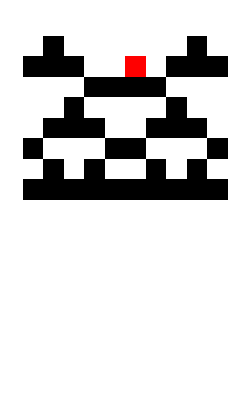

```mathematica
ArrayPlot@swapFunctionNonLinearAutomataColoredniter[54,{0,1,0,0,0,0,0,0,1,0},400,15]
```

In the appendix, many applications of this general perturbation function for different n-iter-dimensional attractive surface are shown.

### Computational Implications of the Perturbation Procedure

In order to perturb the evolution of a cellular automaton and drive it to zero entropy state, we noted how it was essential to first find the ensemble of states that did evolve themselves after some arbitrary iteration time to the zero state. The computational effort required to find these states went as , where   was the number of cells and  the iter-dimension of the attractive surface. As shown in the project, it was possible to reduce the effort required to find these states by stopping the computation after two consecutive n-iter-dimensional attractive surfaces contained the same states. Although accurate results where indeed obtained, this procedure remains an approximation. As the number of states increases, it is not possible for computationally irreducible rules to predict the states contained in the attractive surfaces or somehow skip ahead of the computations. It is, thus, reasonable to assume that as the number of cells increases to infinity, it is simply not possible (or it becomes absurdly computationally difficult)  to determine the initial conditions that lead to a decrease in entropy (or it becomes absurdly difficult) and thus the Third Law of Thermodynamics applies in this limit as a statistical conclusion from the computational shortage that we have available. This lack of information about where to “poke” the cellular automaton to reach a zero entropy state is what, I suggest, we experience as the Third Law of Thermodynamics, in a similar way as the Second Law of Thermodynamics is associated with the impossibility of finding initial conditions that lead to a decrease in entropy [6].  Indeed, when the number of cells is small it is easier to obtain everything we need about the system so that we can apply the perturbations at the right time and positions, but as the automata increases in register size, our loss of knowledge about the system prohibits us to know exactly the right initial conditions or perturbations to apply in order to cool down the system to zero entropy. I propose that this is indeed the reason why the Third Law requires an infinite amount of steps in its definition, as we assume to be able to obtain the right perturbations after infinite trials are made.

## Concluding remarks

The project consisted of defining a procedure to perturb the evolution of a cellular automaton in order to drive it to a zero entropy state with the minimum effort required, effectively acting as refrigerator system. The task was divided by first considering the simpler case of additive cellular automata, where by exploiting the tools of linear algebra it was possible to define a function that accurately solved the problem. The next step was to analyze more general rules, and by introducing the concept of Hamming distance and attractive surface, a perturbation function was again developed to artificially affect the evolution of the system to reach a zero entropy state. Although excellent results were achieved upon application of the function, for the general case, it was not possible to work on registers of size higher than 20-30 cells due to the excessive computational effort required. It was argued that this was a more general instance of the principle of computational irreducibility leading to an eventual lack on information of what perturbations to choose.
Following on the work done, other possible paths of investigation could consist of carrying these perturbation ideas to an application of the Knuth-Bendix algorithm for rewriting systems, where the perturbations applied would be interpreted as performing Knuth-Bendix completions to reach local confluence on a graph and test it its thermodynamical consequences.

## Keywords

Cellular Automata

Thermodynamics

Perturbations

Computational Irreducibility

## Acknowledgment

During the time at the 2022 Wolfram Summer School, I had the possibility to engage and converse with a wide range of great people. In particular, I am grateful to Stephen Wolfram for introducing me to this project and the feedback provided during the course of the School. I am also vastly thankful to both my mentors Jon Lederman and Tom Lee for their constant support, help and time dedicated to me and the project.  Additionally,  I acknowledge and deeply thank Jonathan Gorard for his lectures from which I learned considerably, the exciting daily conversations we had and his invaluable comments that helped shaped the project and the directions pursued. Finally, I must thank all the splendid mentors and students I met during the great time at the Summer School.

## References

[1] Wilks, J. (1971). The Third Law of Thermodynamics, Chapter 6 in Thermodynamics, volume 1, ed. W. Jost, of H. Eyring, D. Henderson, W. Jost, Physical Chemistry. An Advanced Treatise, Academic Press, New York, page 477.

[2] S. Wolfram, “Cellular automata as models of complexity”, Nature 311:419 (1984).

[3] J. Salem and S. Wolfram, Thermodynamics and hydrodynamics with cellular automata, inTheory and Applications of Cellular Automata, S. Wolfram, ed. (World Scientific, 1986).

[4] S. Wolfram, “A New Kind of Science”, 2002, Wolfram Media, Champaign, IL, https://www.wolframscience.com/nks/notes-6-5--additive-cellular-automaton-rules/

[5] S. Wolfram, “A New Kind of Science”, 2002, Wolfram Media, Champaign, IL, https://www.wolframscience.com/nks/notes-6-5--generalized-additivity-in-cellular-automata/

[6] S. Wolfram, "A New Kind of Science", 2002, Wolfram Media, Champaign, IL, https://www.wolframscience.com/nks/p444--irreversibility-and-the-second-law-of-thermodynamics/

## Appendix

### Applications of the Perturbation Function

In this section we display some results obtained by applying the perturbation function defined for driving cellular automata to the zero entropy state. A wide range of rules and initial conditions is selected and the evolution of the cellular automata is plotted.

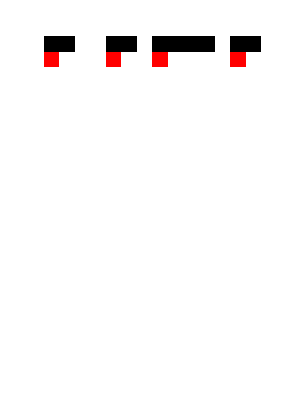
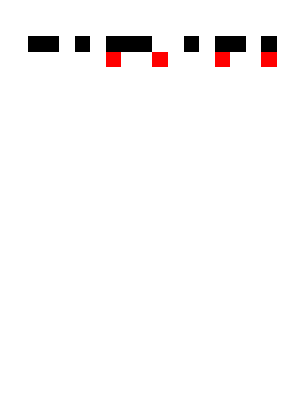
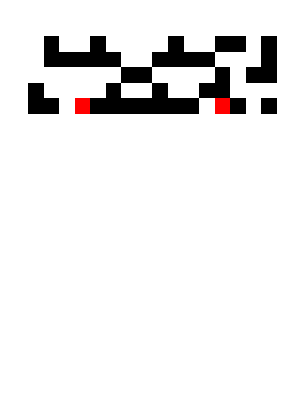
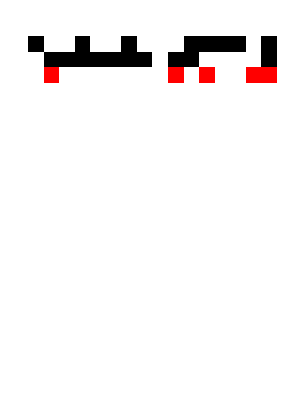
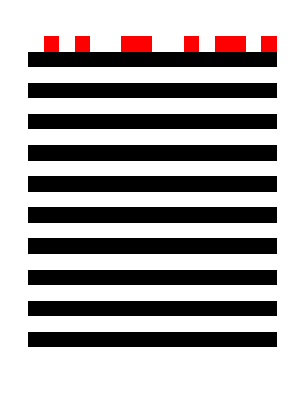
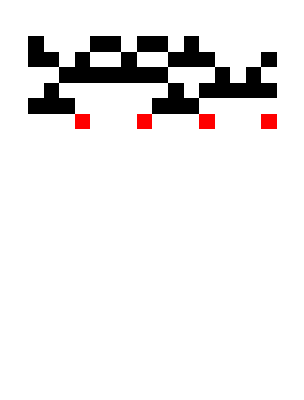
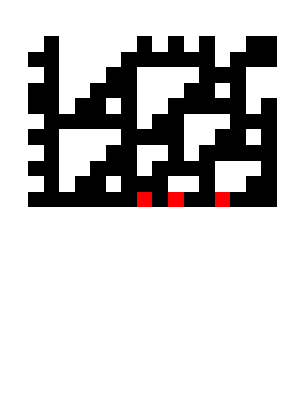
{-Graphics-Rule 8,-Graphics-Rule 128,-Graphics-Rule 12,-Graphics-Rule 24,-Graphics-Rule 22,-Graphics-Rule 30,-Graphics-Rule 90,-Graphics-Rule 105,-Graphics-Rule 54,-Graphics-Rule 110}

```mathematica
ruleslist = {8,128, 12,24,22,30,90,105,54,110};
initrandomlist = Table[RandomInteger[1,16], {i,1,10}];
values =Partition[ Riffle[ruleslist, initrandomlist],2];
Labeled[GraphicsRow[{ArrayPlot@CellularAutomaton[#1,#2, 20],ArrayPlot@swapFunctionNonLinearAutomataColored[#1,#2,20]}], StringJoin["Rule " ,ToString[#1]], Top]&@@@values
```

Reassuringly, the function we defined seems to work well with a wide range of rules and number of cells. It can be seen that some rules may not possess any state in the attractive surface besides the degenerate zero state, therefore the only perturbation which can drive the cellular automata to zero entropy is changing all the cells into white cells. But for such rules, the zero state is highly unstable and gets driven away immediately as the next iteration occurs.

### Applications of the General PerturbationFunction

In this section we display some results obtained by applying the perturbation function defined for driving cellular automata to the zero entropy state for n-iter-dimensional attractive surface. A wide range of rules and initial conditions is selected and the evolution of the perturbed cellular automata is plotted against its normal evolution. Notice how in case a rule does not contain any state in the attractive surface, the cellular automata is driven to the equivalent zero entropy black state.

#### 2-iter-dimensional attractive surface

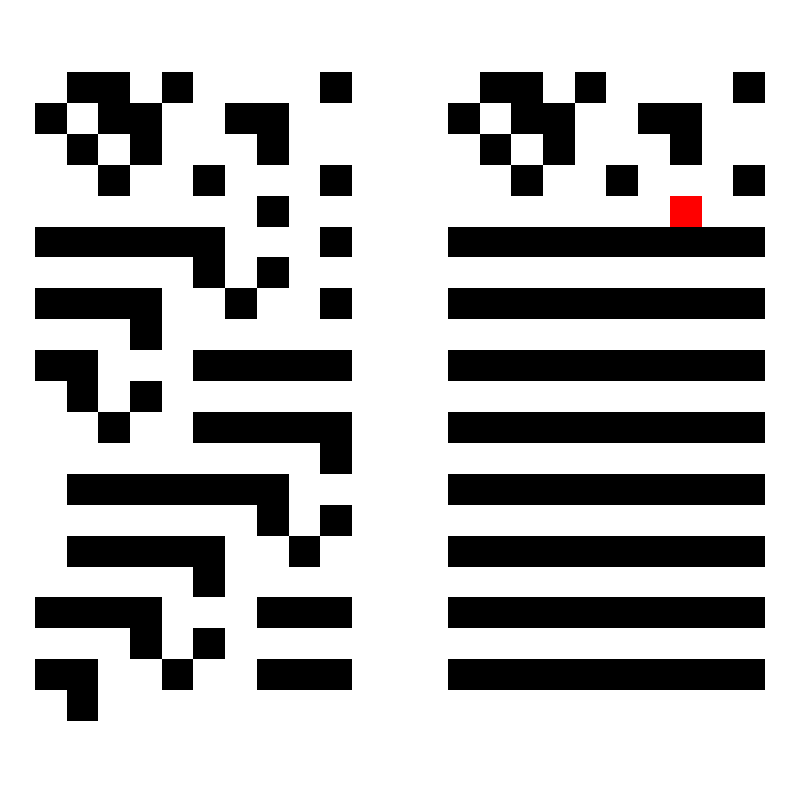
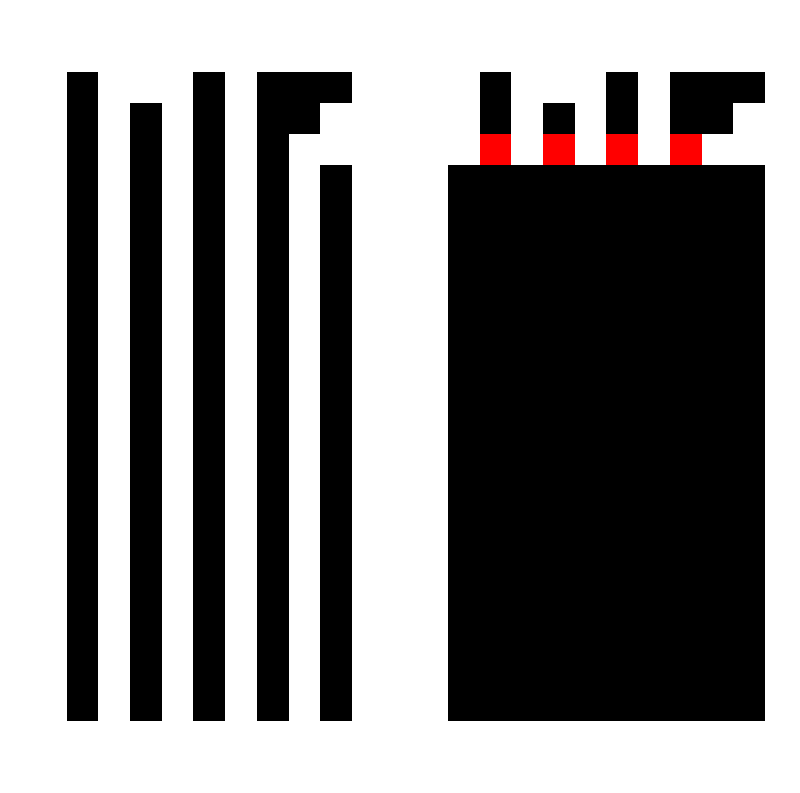
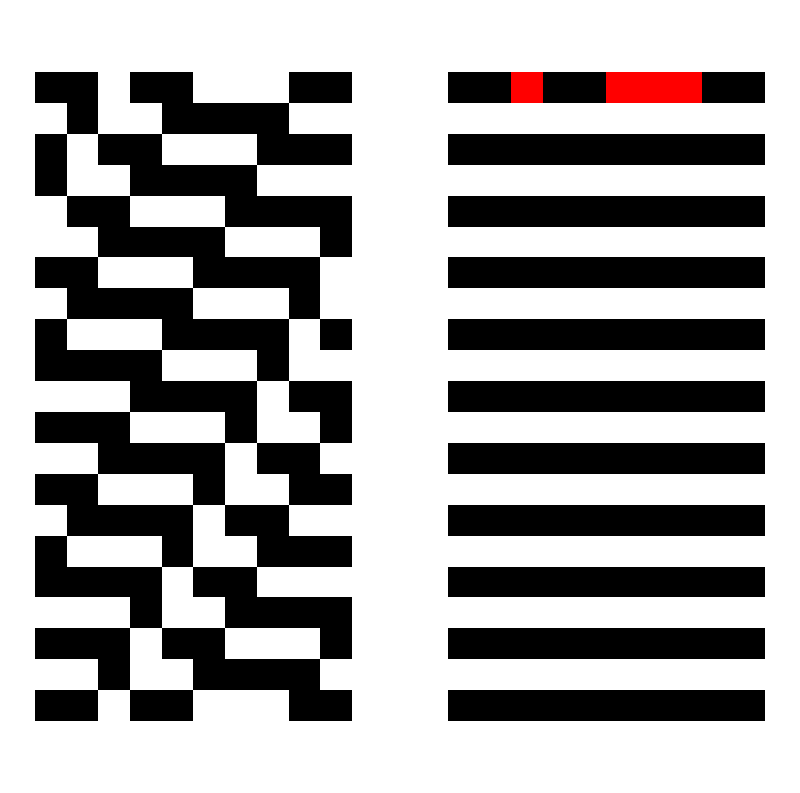
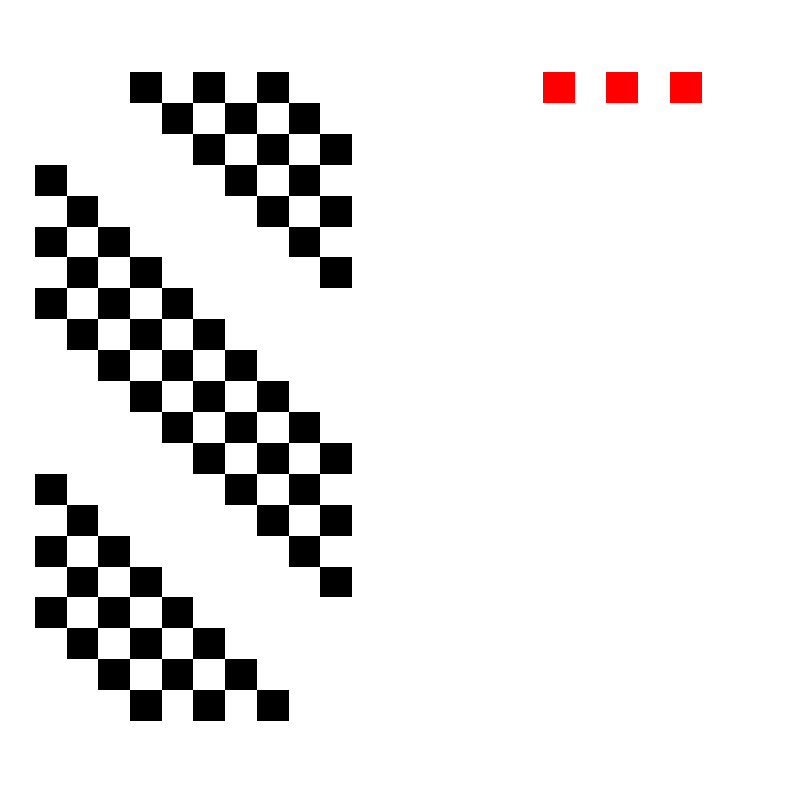
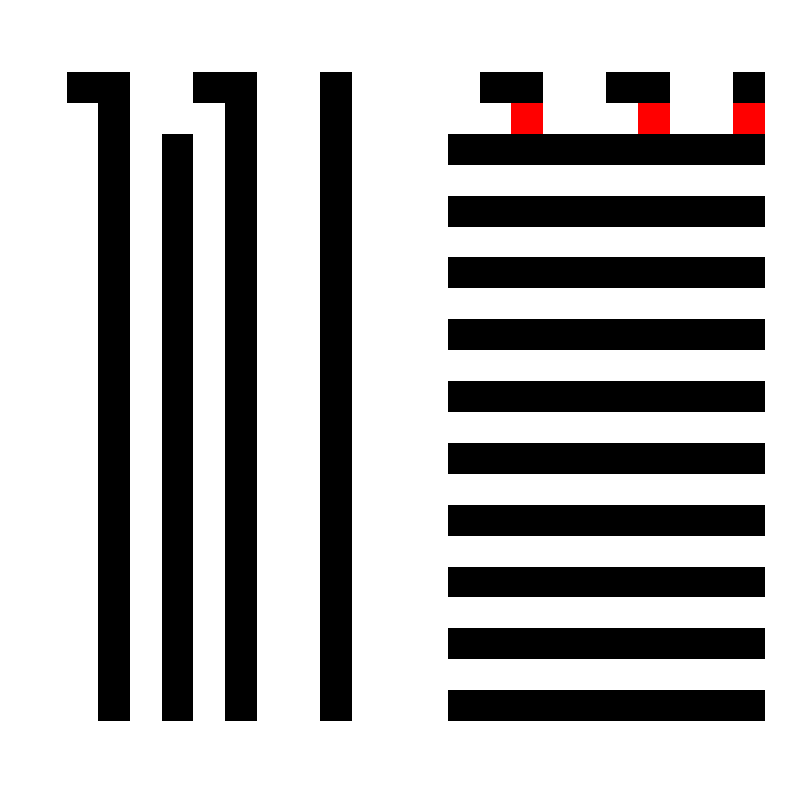
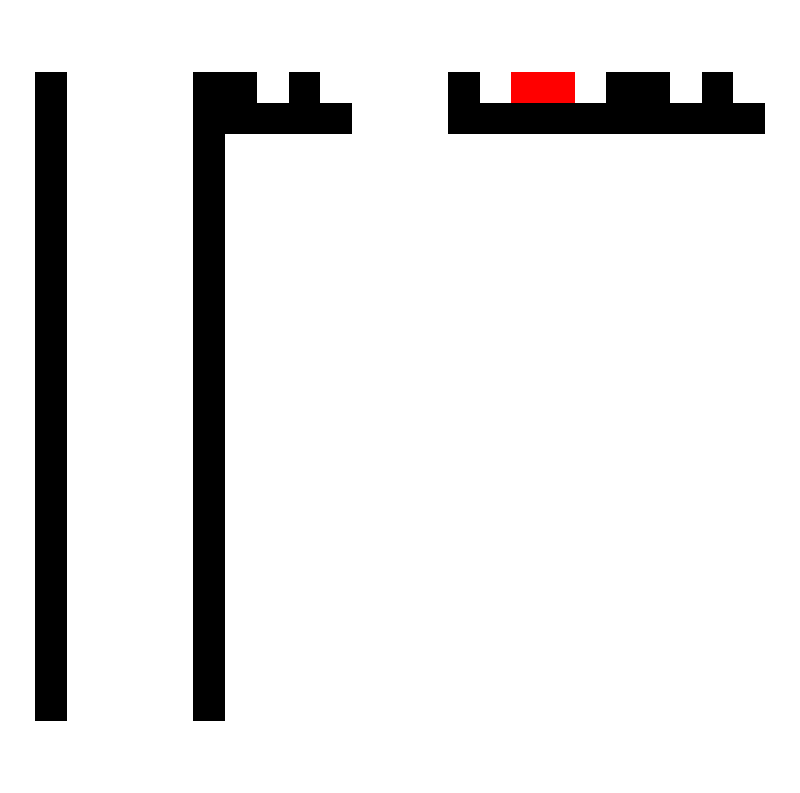
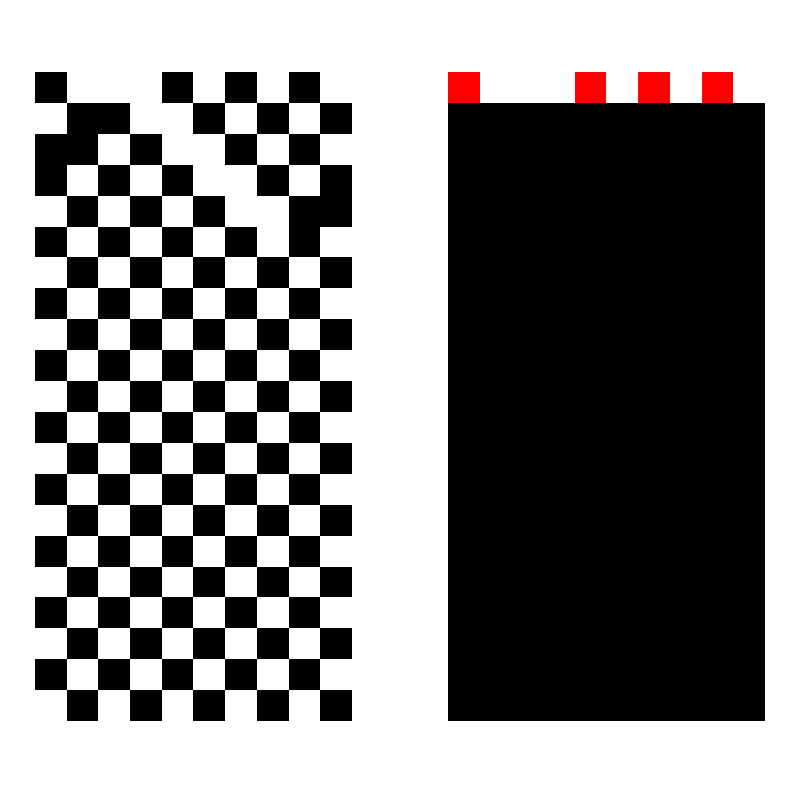
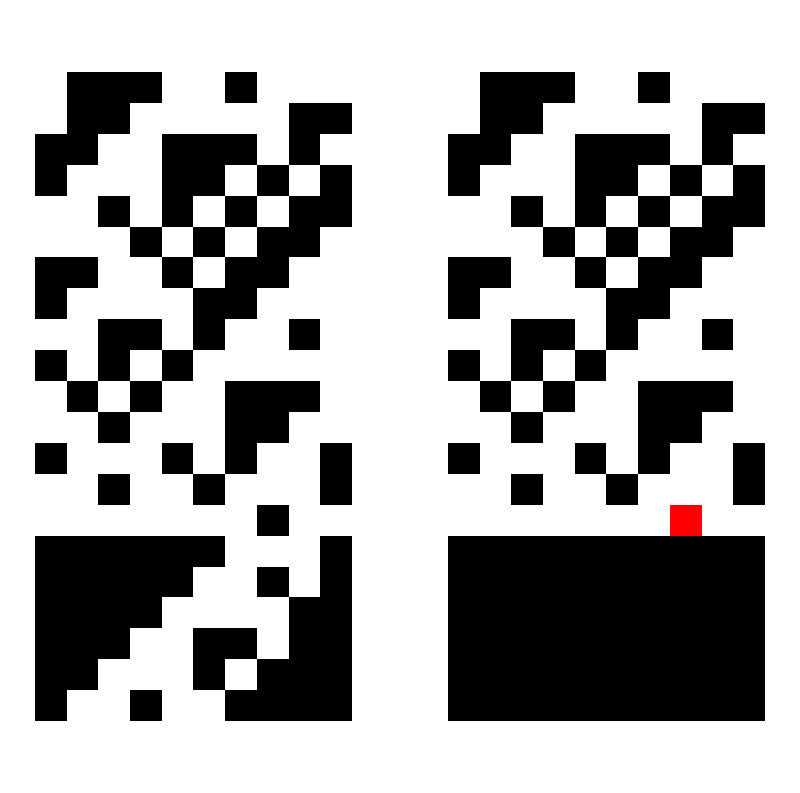
{-Graphics-Rule 97,-Graphics-Rule 141,-Graphics-Rule 83,-Graphics-Rule 240,-Graphics-Rule 69,-Graphics-Rule 108,-Graphics-Rule 185,-Graphics-Rule 169,-Graphics-Rule 12,-Graphics-Rule 199,-Graphics-Rule 95,-Graphics-Rule 228,-Graphics-Rule 166,-Graphics-Rule 183,-Graphics-Rule 200,-Graphics-Rule 146,-Graphics-Rule 145,-Graphics-Rule 204,-Graphics-Rule 187}

```mathematica
SeedRandom[568];
ruleslist2 = RandomInteger[255,20];
initrandomlist2 = Table[RandomInteger[1,10], {i,1,10}];
values2 =Partition[ Riffle[ruleslist2, initrandomlist2],2];
Labeled[GraphicsRow[{ArrayPlot@CellularAutomaton[#1,#2, 20],ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,2,20]}], StringJoin["Rule " ,ToString[#1]], Top]&@@@values2
```

#### 20-iter-dimensional attractive surface

```mathematica
SeedRandom[568];
ruleslist2 = RandomInteger[255,20];
initrandomlist2 = Table[RandomInteger[1,10], {i,1,10}];
values2 =Partition[ Riffle[ruleslist2, initrandomlist2],2];
Labeled[GraphicsRow[{ArrayPlot@CellularAutomaton[#1,#2, 20],ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,20,20]}], StringJoin["Rule " ,ToString[#1]], Top]&@@@values2
```

{-Graphics-Rule 97,-Graphics-Rule 141,-Graphics-Rule 83,-Graphics-Rule 240,-Graphics-Rule 69,-Graphics-Rule 108,-Graphics-Rule 185,-Graphics-Rule 169,-Graphics-Rule 12,-Graphics-Rule 199,-Graphics-Rule 95,-Graphics-Rule 228,-Graphics-Rule 166,-Graphics-Rule 183,-Graphics-Rule 200,-Graphics-Rule 146,-Graphics-Rule 145,-Graphics-Rule 204,-Graphics-Rule 187}

#### Comparison 1-iter and n-iter Perturbations

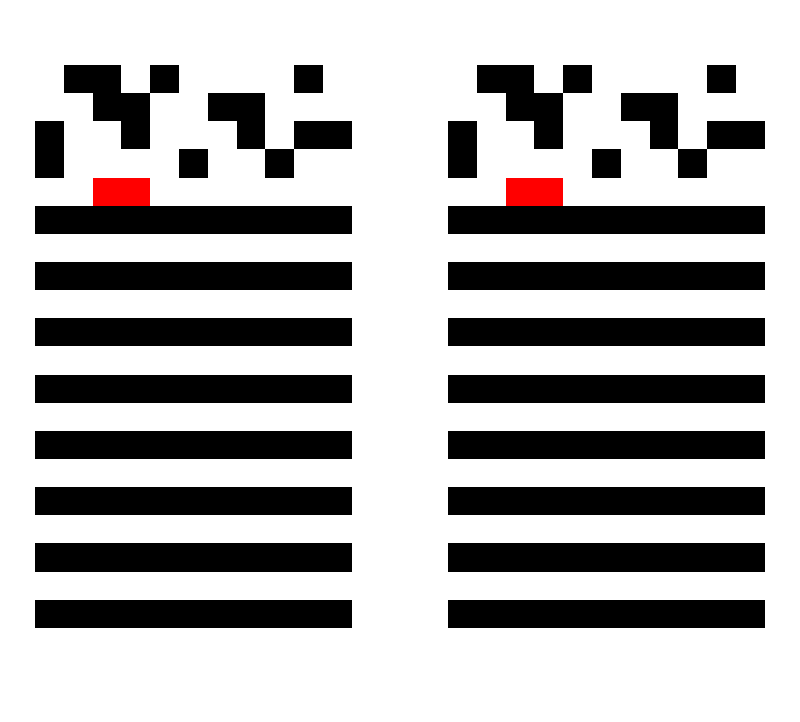
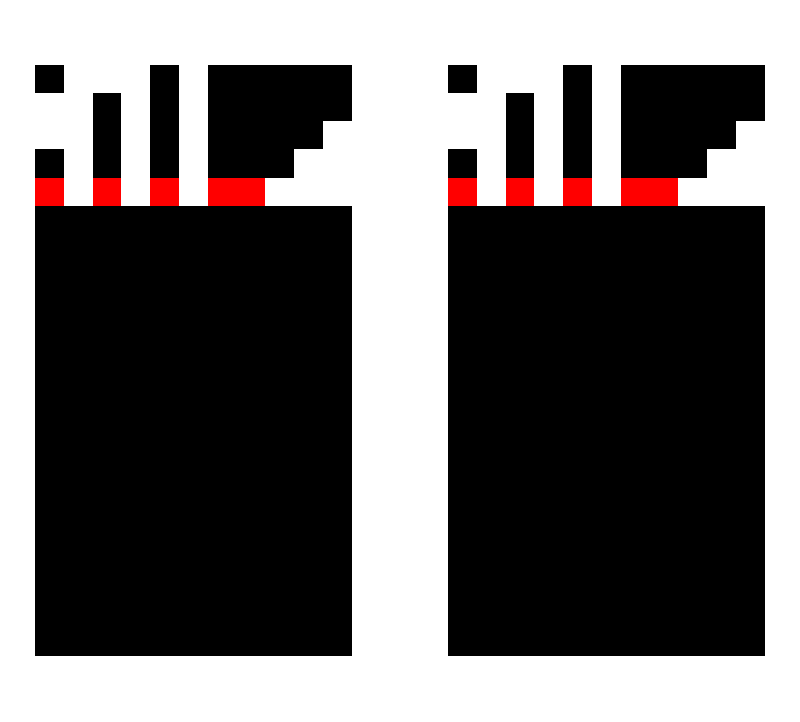
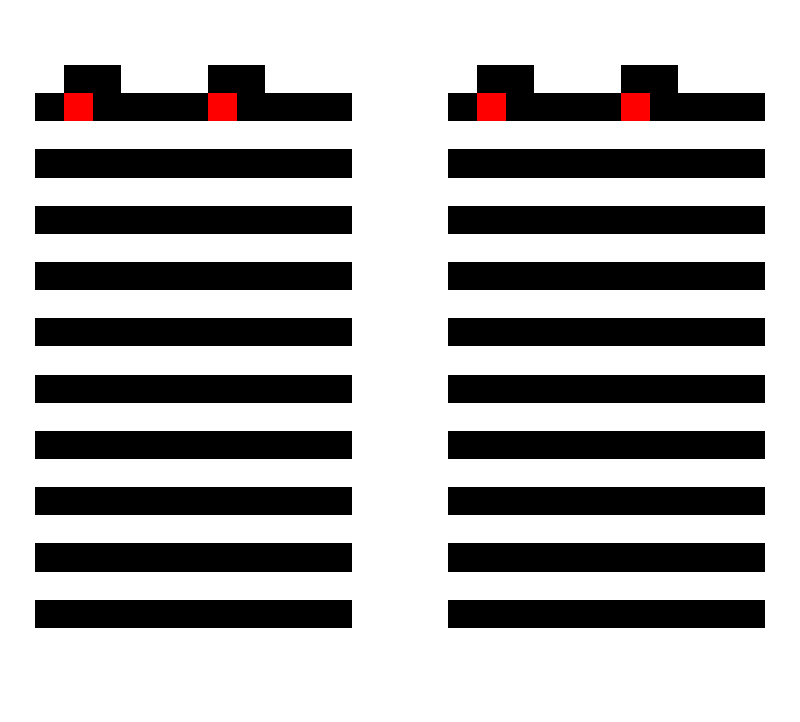
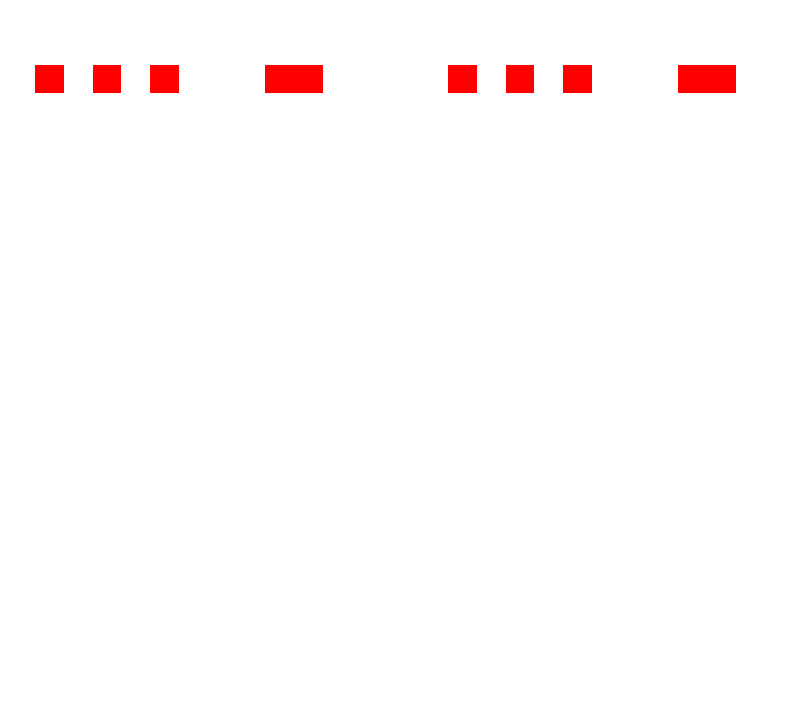
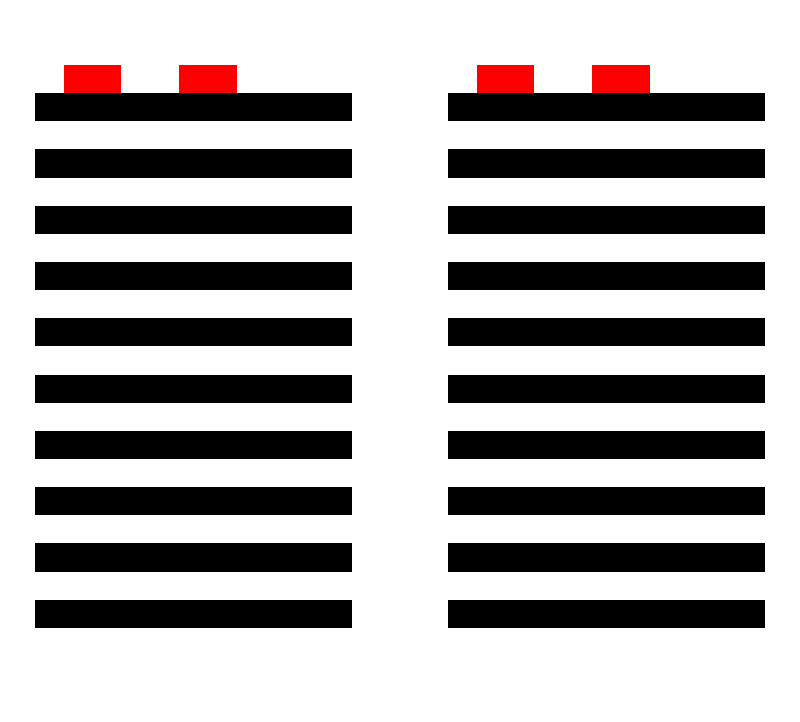
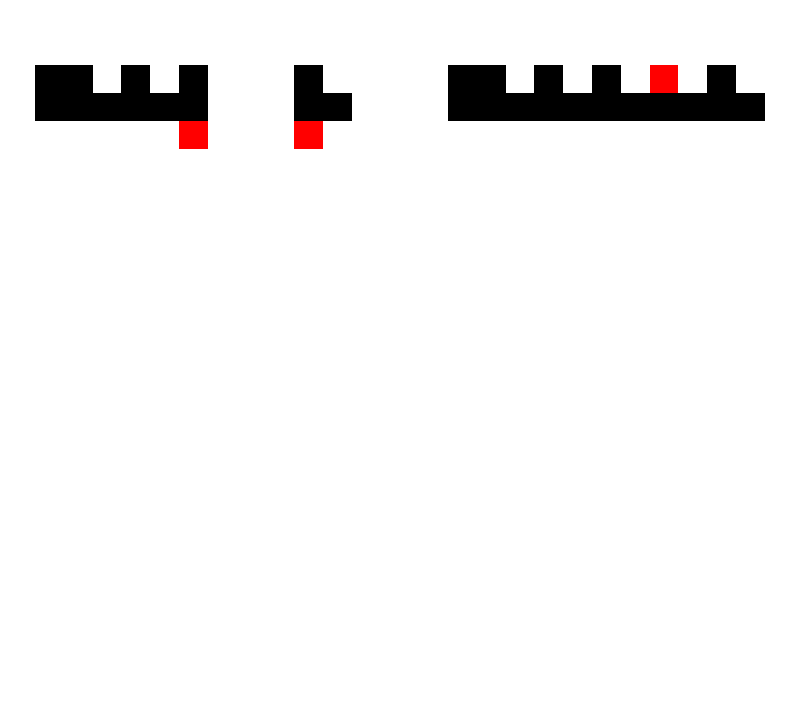
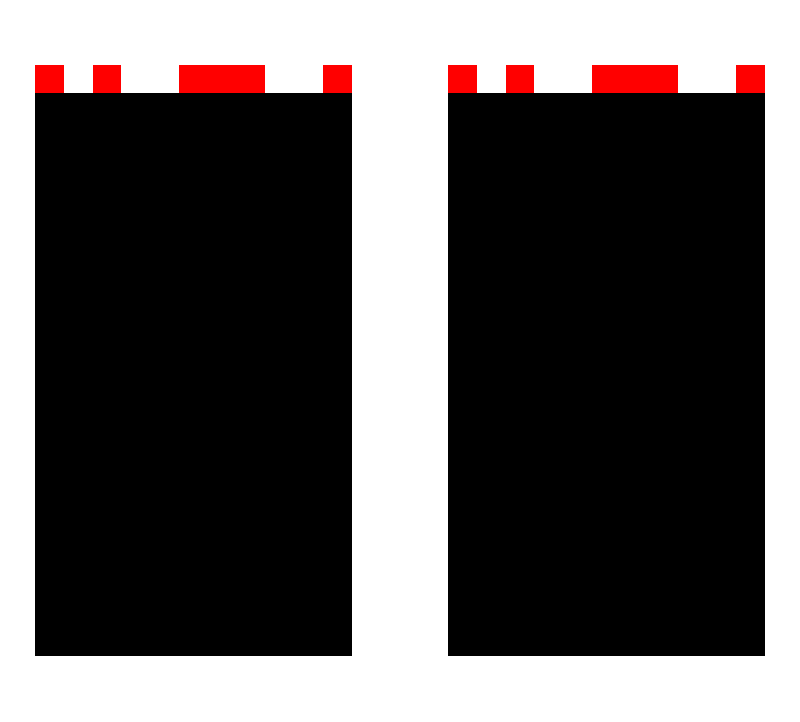
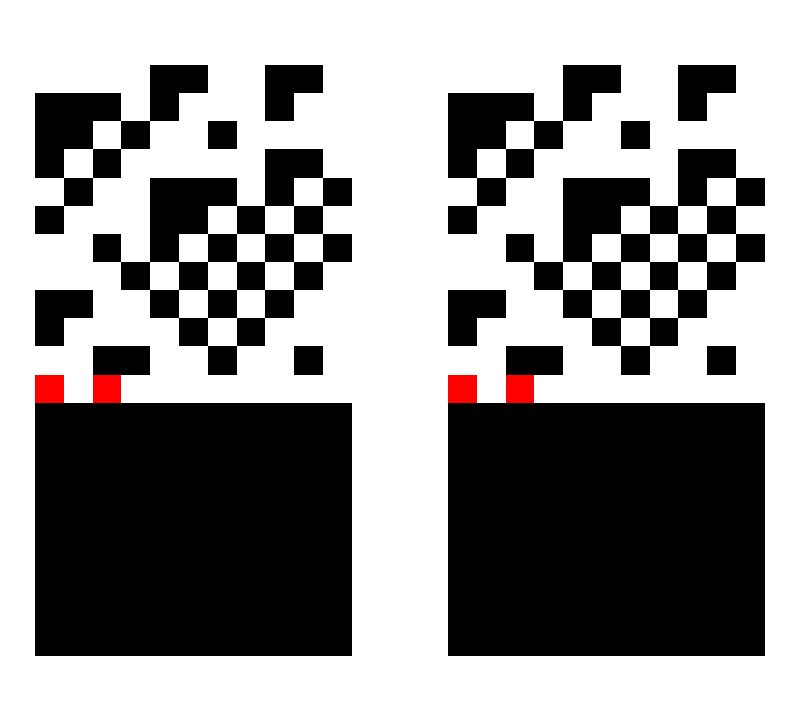
{-Graphics-Rule 97,-Graphics-Rule 141,-Graphics-Rule 83,-Graphics-Rule 240,-Graphics-Rule 69,-Graphics-Rule 108,-Graphics-Rule 185,-Graphics-Rule 169,-Graphics-Rule 12,-Graphics-Rule 199,-Graphics-Rule 95,-Graphics-Rule 228,-Graphics-Rule 166,-Graphics-Rule 183,-Graphics-Rule 200,-Graphics-Rule 146,-Graphics-Rule 145,-Graphics-Rule 204,-Graphics-Rule 187,-Graphics-Rule 191}

```mathematica
SeedRandom[568];
ruleslist2 = RandomInteger[255,20];
initrandomlist2 = Table[RandomInteger[1,11], {i,1,20}];
values2 =Partition[ Riffle[ruleslist2, initrandomlist2],2];
Labeled[GraphicsRow[{ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,1, 20],ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,10,20]}], StringJoin["Rule " ,ToString[#1]], Top]&@@@values2
```

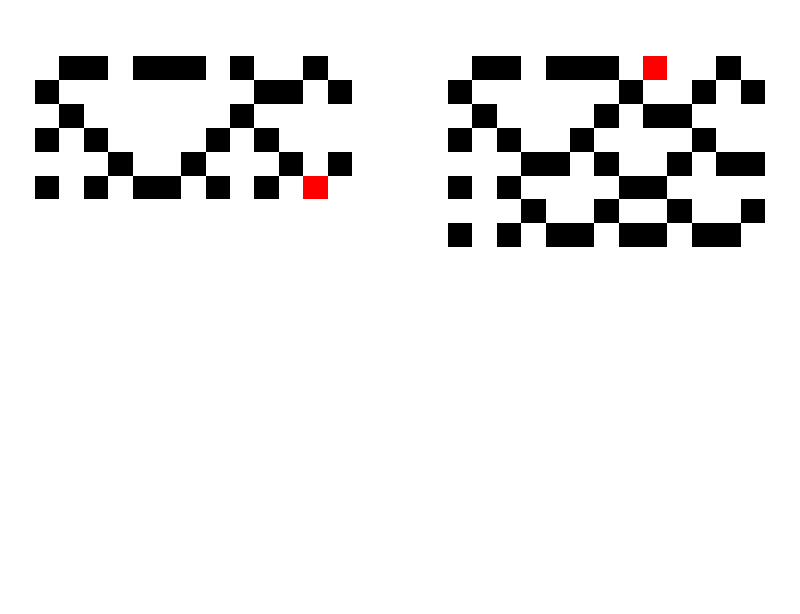
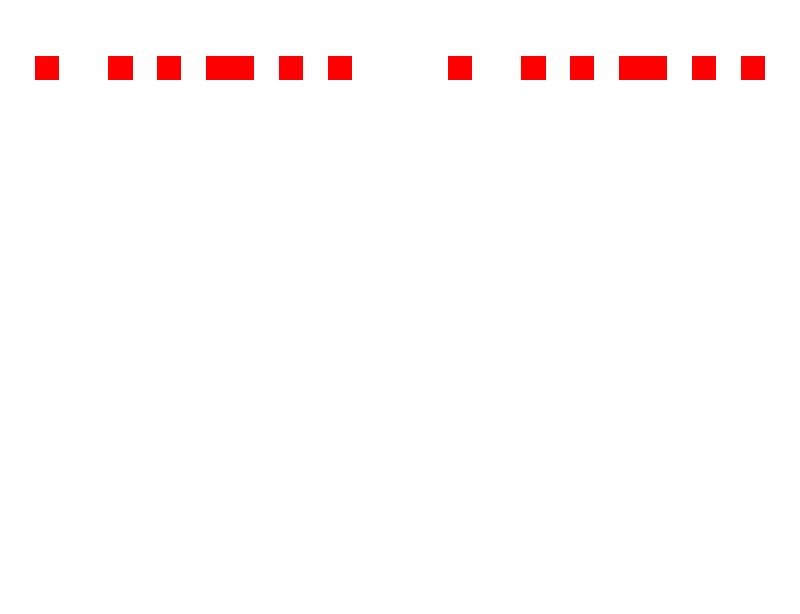
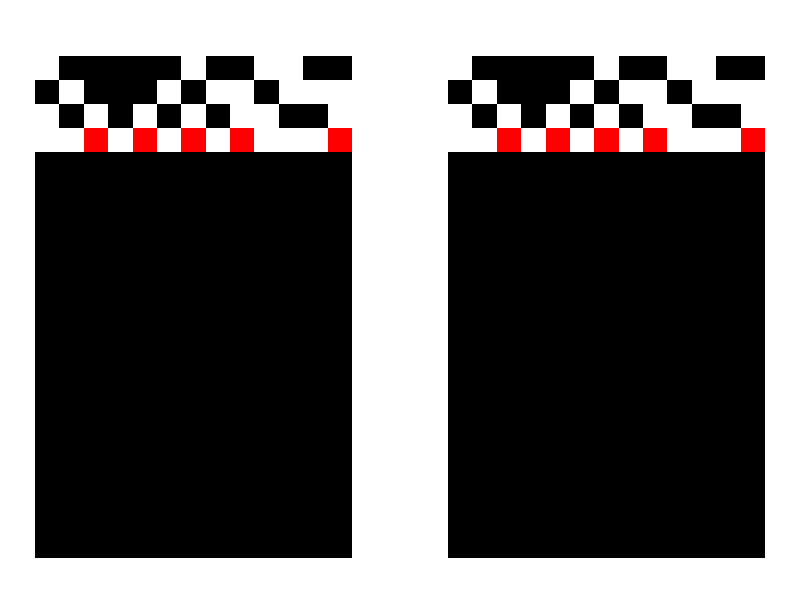
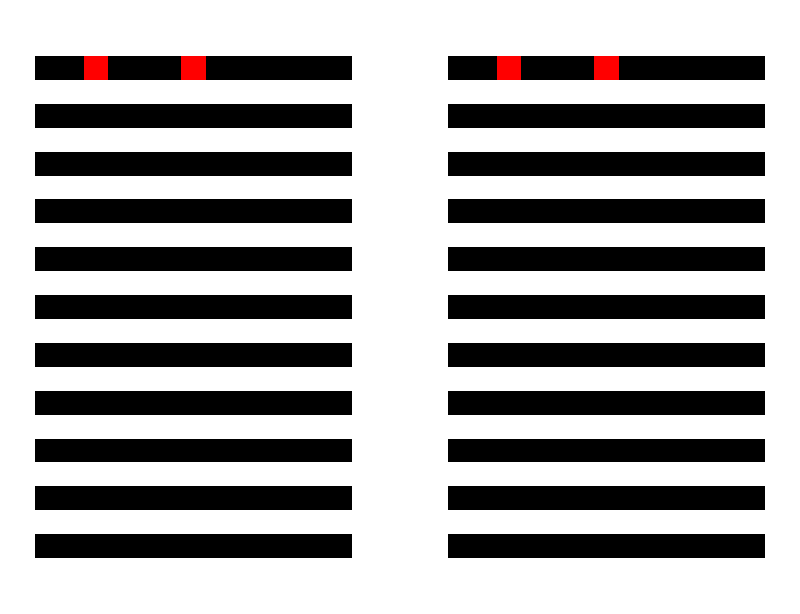
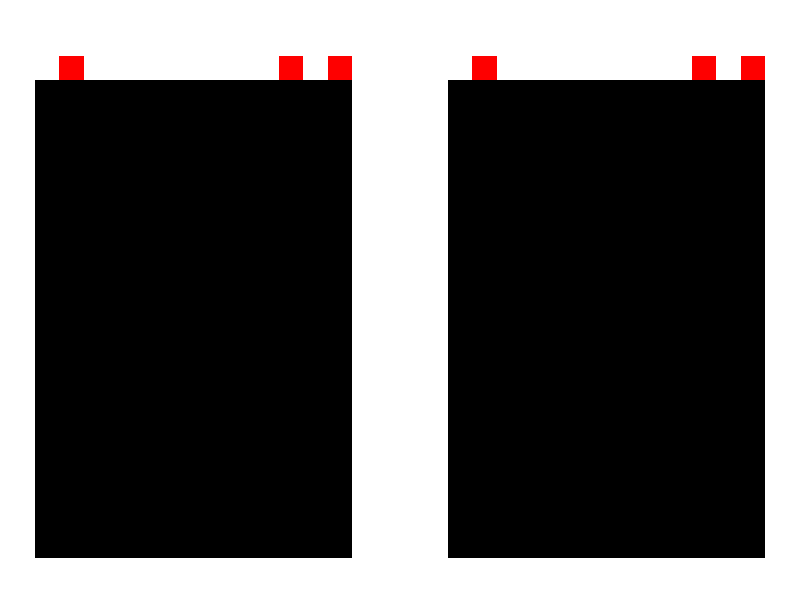
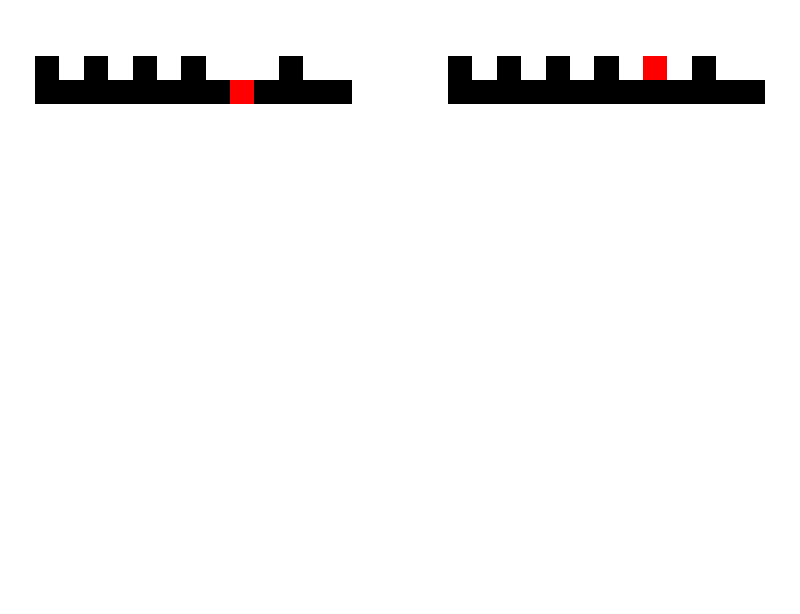
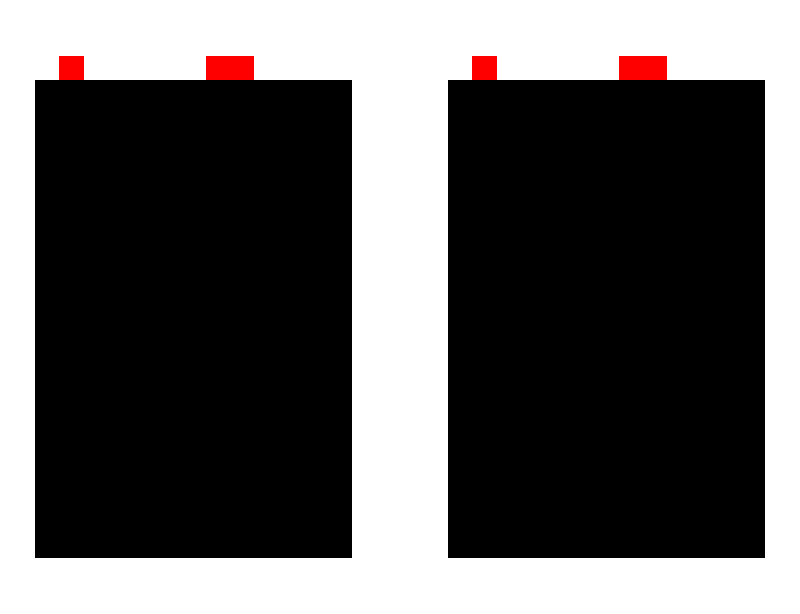
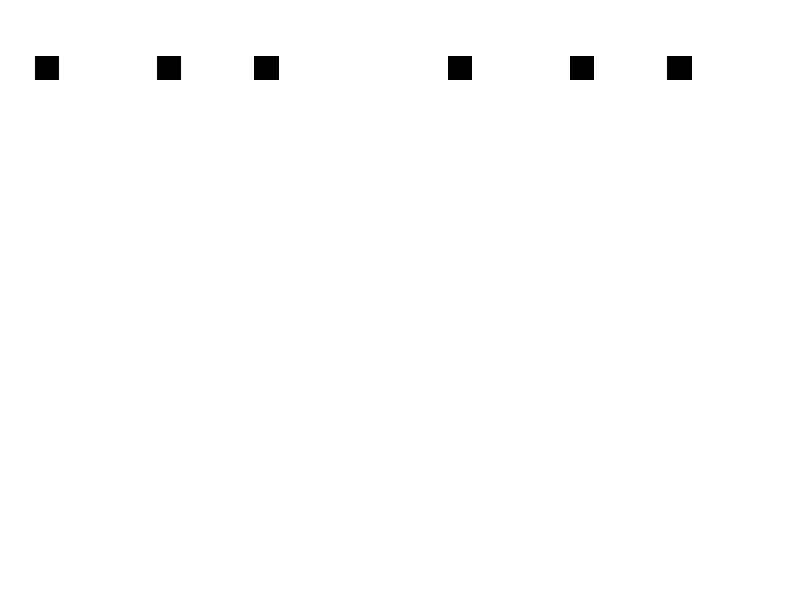
{-Graphics-Rule 18,-Graphics-Rule 238,-Graphics-Rule 177,-Graphics-Rule 95,-Graphics-Rule 249,-Graphics-Rule 118,-Graphics-Rule 157,-Graphics-Rule 104,-Graphics-Rule 31,-Graphics-Rule 193,-Graphics-Rule 211,-Graphics-Rule 12,-Graphics-Rule 170,-Graphics-Rule 198,-Graphics-Rule 119,-Graphics-Rule 122,-Graphics-Rule 238,-Graphics-Rule 237,-Graphics-Rule 71,-Graphics-Rule 117}

```mathematica
SeedRandom[400];
ruleslist2 = RandomInteger[255,20];
initrandomlist2 = Table[RandomInteger[1,13], {i,1,20}];
values2 =Partition[ Riffle[ruleslist2, initrandomlist2],2];
Labeled[GraphicsRow[{ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,1, 20],ArrayPlot@swapFunctionNonLinearAutomataColoredniter[#1,#2,10,20]}], StringJoin["Rule " ,ToString[#1]], Top]&@@@values2
```